```mathematica
模型G-模型N
```

```mathematica
品牌商期望利润：
```

```mathematica
ClearAll[a,k,θ,ρ,σ]
```

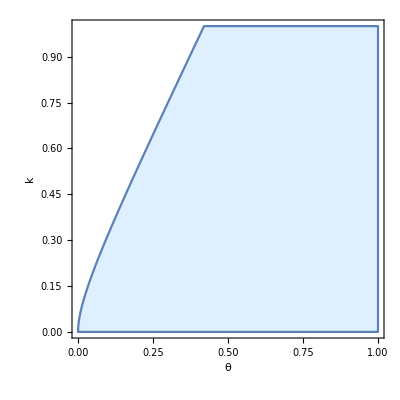

```mathematica
a=0.8;
ρ=0.5;
RegionPlot[{-((a^2 (-1+ρ) (2 k^2 (-4+θ+3 θ ρ)-4 k θ (-4+θ+3 θ ρ)+θ (6-6 ρ+θ (-2+θ (-1+3 ρ)))))/(8 (-4+θ+3 θ ρ) (2 (-1+ρ)+θ (-2+θ+θ ρ))))>0},{θ,0,1},{k,0,1},FrameLabel->{θ,k},PlotStyle->LightBlue,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

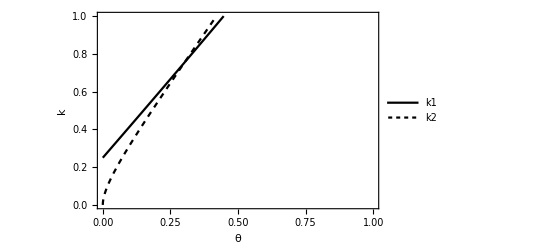

```mathematica
a=0.8;
ρ=0.5;
Plot[{(2 (-1+ρ+θ (-3+θ+2 θ ρ)))/(-4+θ+3 θ ρ),θ-(√(3/2) √(θ (-4+θ+3 θ ρ) (2 (-1+ρ)+θ (-2+θ+θ ρ))))/(-4+θ+3 θ ρ)},{θ,0,1},Frame->True,FrameLabel->{θ,k},FrameTicks->Automatic,PlotLegends->Placed[{k1,k2,k3},Right],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],PlotStyle->{Black,{Dashing [0.01],Black},{Dashing [0.01],Black}},PlotRange->{0,1}]
```

```mathematica
ClearAll[a,k,θ,ρ,σ]
```

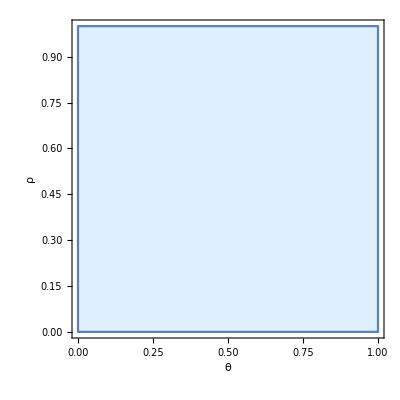

```mathematica
a=0.8;
k=0.5;
RegionPlot[{1/8 a^2 (-2 k+(2+k θ)^2/(2+θ^2)-(4 (-1+θ))/(-4+θ+3 θ ρ)+(4 (k-θ)^2 (-1+θ) θ)/((2+θ^2) (2 (-1+ρ)+θ (-2+θ+θ ρ))))>0},{θ,0,1},{ρ,0,1},FrameLabel->{θ,ρ},PlotStyle->LightBlue,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
零售商L期望利润：
```

```mathematica
ClearAll[a,k,θ,ρ,σ]
```

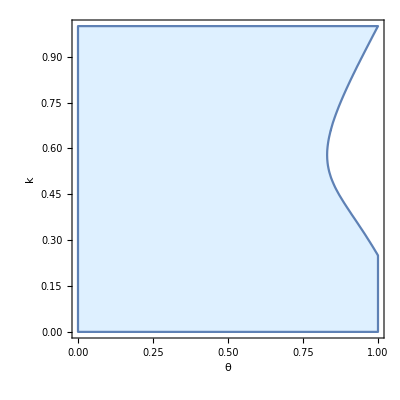

```mathematica
a=0.8;
ρ=0.4;
σ=0.3;
RegionPlot[{1/(4 (-4+θ+3 θ ρ)^2)(-1+ρ) (1/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2 a^2 (k^2 (-4+θ+3 θ ρ)^2 (3 (-1+ρ)+θ (-3+θ (2+ρ)))-k θ (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+θ (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ)))))+4 (-1+θ) θ σ^2)>0},{θ,0,1},{k,0,1},FrameLabel->{θ,k},PlotStyle->LightBlue,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

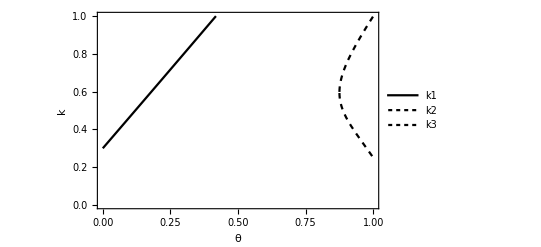

```mathematica
a=0.8;
ρ=0.4;
A=0.2;
Plot[{(2 (-1+ρ+θ (-3+θ+2 θ ρ)))/(-4+θ+3 θ ρ),(a θ (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-√θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) √(a^2 (12 (-1+ρ)+θ (4-12 ρ+θ (24-7 θ-2 (4+5 θ) ρ+9 θ ρ^2)))-16 (-1+θ) (3 (-1+ρ)+θ (-3+θ (2+ρ))) A))/(2 a (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))),(a θ (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+√θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) √(a^2 (12 (-1+ρ)+θ (4-12 ρ+θ (24-7 θ-2 (4+5 θ) ρ+9 θ ρ^2)))-16 (-1+θ) (3 (-1+ρ)+θ (-3+θ (2+ρ))) A))/(2 a (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ))))},{θ,0,1},Frame->True,FrameLabel->{θ,k},FrameTicks->Automatic,PlotLegends->Placed[{k1,k2,k3},Right],LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],PlotStyle->{Black,{Dashing [0.01],Black},{Dashing [0.01],Black}},PlotRange->{0,1}]
```

```mathematica
--------------------------------------------------
```

```mathematica
品牌商期望利润：   模型B(此时品牌商知道信息但cg外生)-模型G
```

```mathematica
FullSimplify[1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))-((a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))))/(8 (-4+θ+3 θ ρ) (2 (-1+ρ)+θ (-2+θ+θ ρ))))]
```

1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))

```mathematica
ClearAll[a,d,k,θ,ρ,σ,cm,cg]
```

```mathematica
Manipulate[Plot[1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))),{cg,0,0.5}],{ρ,0,1},{a,0,1},{k,0,1},{σ,0,1},{cb,0,0.15},{θ,0,1}]
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

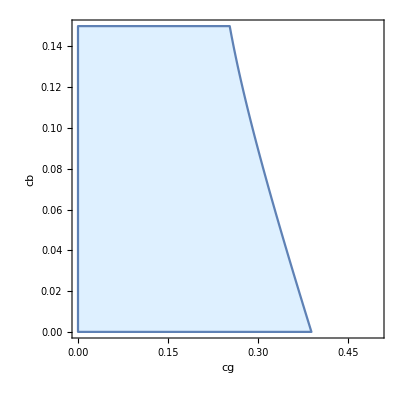

```mathematica
a=0.8;
k=0.4;
θ=0.7;
ρ=0.4;
σ=0.3;
RegionPlot[{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))>0},{cg,0,0.5},{cb,0,0.15},FrameLabel->{cg,cb},PlotStyle->LightBlue,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
看ρ的影响：
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

```mathematica
a=0.8;
k=0.4;
θ=0.5;
A=0.2;
Show[ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{ρ->0.2}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.02],PlotLegends->Placed[{"ρ=0.3"},{Left,Center}]],ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{ρ->0.5}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.01],PlotLegends->Placed[{"ρ=0.5"},{Left,Center}]],ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{ρ->0.8}}==0},{cg,0,0.5},{cb,0,0.25},PlotLegends->Placed[{"ρ=0.7"},{Left,Center}]],
FrameLabel->{Subscript[C, g],Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

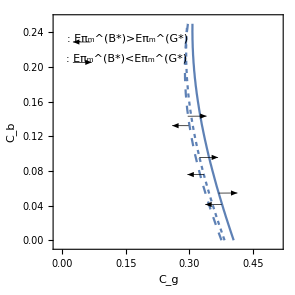

```mathematica
看σ.b2的影响：
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

```mathematica
a=0.8;
k=0.4;
θ=0.5;
ρ=0.5;
Show[ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{A->0.1}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.02],PlotLegends->Placed[{"σ^2=0.1"},{Left,Center}]],ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{A->0.2}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.01],PlotLegends->Placed[{"σ^2=0.2"},{Left,Center}]],ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{A->0.3}}==0},{cg,0,0.5},{cb,0,0.25},PlotLegends->Placed[{"σ^2=0.3"},{Left,Center}]],
FrameLabel->{Subscript[C, g],Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

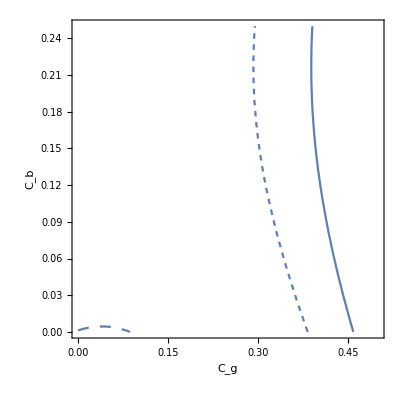

```mathematica
a=0.8;
k=0.4;
θ=0.5;
ρ=0.5;
Show[ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{A->0.001}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.02],PlotLegends->Placed[{"σ^2=0"},{Left,Center}]],ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{A->0.2}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.01],PlotLegends->Placed[{"σ^2=0.2"},{Left,Center}]],ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{A->0.3}}==0},{cg,0,0.5},{cb,0,0.25},PlotLegends->Placed[{"σ^2=0.3"},{Left,Center}]],
FrameLabel->{"C_g","C_b"},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

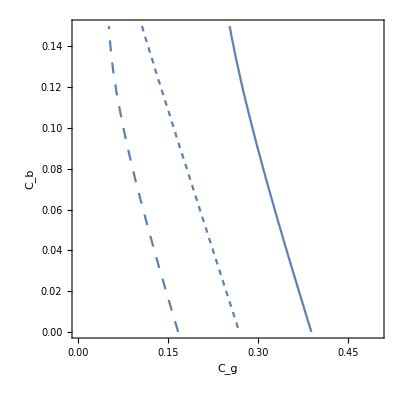

```mathematica
a=0.8;
k=0.4;
ρ=0.4;
σ=0.3;
Show[ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{θ->0.3}}==0},{cg,0,0.5},{cb,0,0.15},ContourStyle->Dashing[0.02],PlotLegends->Placed[{"θ=0.3"},{Left,Center}]],ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{θ->0.5}}==0},{cg,0,0.5},{cb,0,0.15},ContourStyle->Dashing[0.01],PlotLegends->Placed[{"θ=0.5"},{Left,Center}]],ContourPlot[{{1/8 (-2 a cb k-(4 a cb (-1+ρ))/(-4+θ+3 θ ρ)-(8 a cg (k-θ) (-1+ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+1/(-4+θ+3 θ ρ)((cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))))/.{θ->0.7}}==0},{cg,0,0.5},{cb,0,0.15},PlotLegends->Placed[{"θ=0.7"},{Left,Center}]],
FrameLabel->{Subscript[C, g],Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
零售商L期望利润：   模型B(此时品牌商知道信息但cg外生)-模型G
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

```mathematica
FullSimplify[(cb^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))-2 cb (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)-2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))+a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ))))+(-1+θ) θ (16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))+(k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))) (a^2+σ^2)))/(16 (-1+θ) θ (-4+θ+3 θ ρ)^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2)-(1/(16 (-4+θ+3 θ ρ)^2)((a^2 (k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2+4 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) σ^2))]
```

1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)

```mathematica
ClearAll[a,d,k,θ,ρ,σ,cm,cg]
```

```mathematica
Manipulate[Plot[1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2),{cg,0,0.5}],{ρ,0,1},{a,0,1},{k,0,1},{σ,0,1},{cb,0,0.15},{θ,0,1}]
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

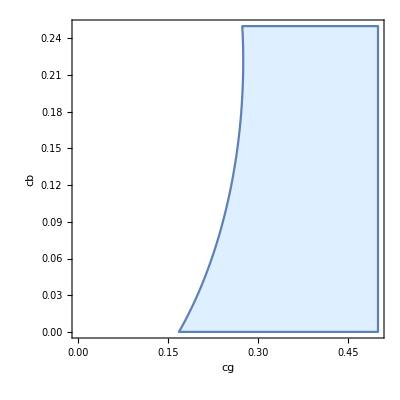

```mathematica
a=0.8;
k=0.4;
θ=0.5;
ρ=0.4;
σ=0.4;
RegionPlot[{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)>0},{cg,0,0.5},{cb,0,0.25},FrameLabel->{cg,cb},PlotStyle->LightBlue,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
看ρ的影响
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

```mathematica
a=0.8;
k=0.4;
θ=0.5;
A=0.2;
Show[ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{ρ->0.3}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.02],PlotLegends->Placed[{"ρ=0.3"},{Left,Center}]],ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{ρ->0.5}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.01],PlotLegends->Placed[{"ρ=0.5"},{Left,Center}]],ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{ρ->0.7}}==0},{cg,0,0.5},{cb,0,0.25},PlotLegends->Placed[{"ρ=0.7"},{Left,Center}]],
FrameLabel->{Subscript[C, g],Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

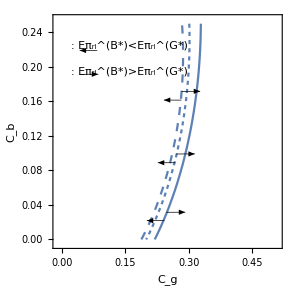

```mathematica
看σ.b2的影响：
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

```mathematica
a=0.8;
k=0.4;
θ=0.5;
ρ=0.5;
Show[ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{A->0.1}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.02],PlotLegends->Placed[{"σ^2=0.1"},{Left,Center}]],ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{A->0.2}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.01],PlotLegends->Placed[{"σ^2=0.2"},{Left,Center}]],ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{A->0.3}}==0},{cg,0,0.5},{cb,0,0.25},PlotLegends->Placed[{"σ^2=0.3"},{Left,Center}]],
FrameLabel->{Subscript[C, g],Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

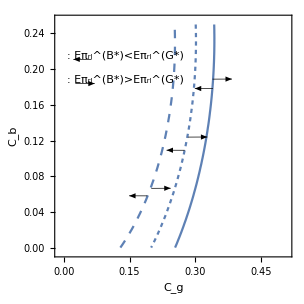

```mathematica
看θ的影响：
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

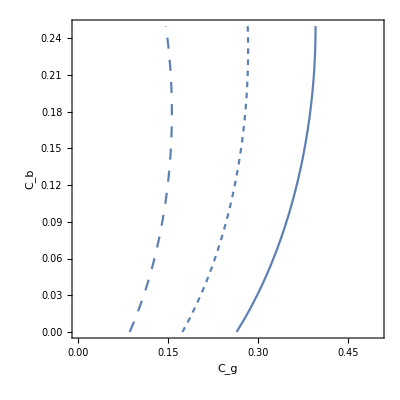

```mathematica
a=0.8;
k=0.4;
ρ=0.5;
σ=0.4;
Show[ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{θ->0.3}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.02],PlotLegends->Placed[{"θ=0.3"},{Left,Center}]],ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{θ->0.5}}==0},{cg,0,0.5},{cb,0,0.25},ContourStyle->Dashing[0.01],PlotLegends->Placed[{"θ=0.5"},{Left,Center}]],ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)((cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)+(2 cb (-4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)+2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))-a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))+(16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))-θ (k^2 (-4+θ+3 θ ρ)^2 (-12 (-1+ρ)+θ (8-4 ρ+8 ρ^2-12 θ (1+ρ)+3 θ^2 (1+ρ)^2))+4 k (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))-4 (-1+ρ) (12 (-1+ρ)^2-4 θ (-1+ρ) (-5+3 ρ)+4 θ^5 ρ (2+3 ρ)-4 θ^2 (7-8 ρ+6 ρ^2)-4 θ^4 (2+ρ (10+3 ρ))+θ^3 (35+ρ (19-3 ρ+9 ρ^2)))) σ^2)/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{θ->0.7}}==0},{cg,0,0.5},{cb,0,0.25},PlotLegends->Placed[{"θ=0.7"},{Left,Center}]],
FrameLabel->{Subscript[C, g],Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
零售商H利润：模型B(此时品牌商知道信息但cg外生)-模型G
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

```mathematica
FullSimplify[(((-1+θ ρ) ((2 a (-1+θ)+cb (-1+ρ))^2+4 (-1+θ)^2 σ^2))/(4 (-1+θ) (-4+θ+3 θ ρ)^2))-(((-1+θ) (-1+θ ρ) (a^2+4 σ^2))/(-4+θ+3 θ ρ)^2)]
```

((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 σ^2))/(4 (-1+θ) (-4+θ+3 θ ρ)^2)

```mathematica
Manipulate[Plot[((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 σ^2))/(4 (-1+θ) (-4+θ+3 θ ρ)^2),{cb,0,0.25}],{ρ,0,1},{a,0,1},{σ,0,1},{θ,0,1}]
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

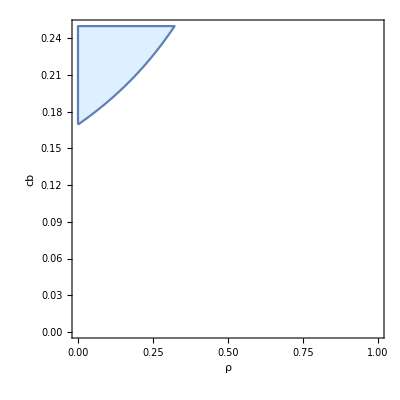

```mathematica
a=0.8;
θ=0.5;
A=0.1;
RegionPlot[{((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 A))/(4 (-1+θ) (-4+θ+3 θ ρ)^2)>0},{ρ,0,1},{cb,0,0.25},FrameLabel->{ρ,cb},PlotStyle->LightBlue,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

```mathematica
a=0.8;
θ=0.5;
Show[ContourPlot[{{((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 A))/(4 (-1+θ) (-4+θ+3 θ ρ)^2)/.{A->0.04}}==0},{ρ,0,1},{cb,0,0.25},ContourStyle->Dashing[0.02],PlotLegends->Placed[{"σ^2=0.04"},{Left,Center}]],ContourPlot[{{((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 A))/(4 (-1+θ) (-4+θ+3 θ ρ)^2)/.{A->0.08}}==0},{ρ,0,1},{cb,0,0.25},ContourStyle->Dashing[0.01],PlotLegends->Placed[{"σ^2=0.08"},{Left,Center}]],ContourPlot[{{((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 A))/(4 (-1+θ) (-4+θ+3 θ ρ)^2)/.{A->0.12}}==0},{ρ,0,1},{cb,0,0.25},PlotLegends->Placed[{"σ^2=0.12"},{Left,Center}]],
FrameLabel->{ρ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

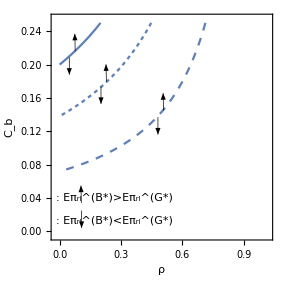

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

```mathematica
a=0.8;
A=0.08;
Show[ContourPlot[{{((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 A))/(4 (-1+θ) (-4+θ+3 θ ρ)^2)/.{θ->0.2}}==0},{ρ,0,1},{cb,0,0.25},ContourStyle->Dashing[0.02],PlotLegends->Placed[{"θ=0.2"},{Left,Center}]],ContourPlot[{{((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 A))/(4 (-1+θ) (-4+θ+3 θ ρ)^2)/.{θ->0.4}}==0},{ρ,0,1},{cb,0,0.25},ContourStyle->Dashing[0.01],PlotLegends->Placed[{"θ=0.4"},{Left,Center}]],ContourPlot[{{((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 A))/(4 (-1+θ) (-4+θ+3 θ ρ)^2)/.{θ->0.6}}==0},{ρ,0,1},{cb,0,0.25},PlotLegends->Placed[{"θ=0.6"},{Left,Center}]],
FrameLabel->{ρ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

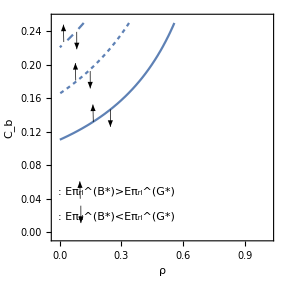

```mathematica
----------------------------------------------------------------
```

```mathematica
Extended  Model:
```

```mathematica
品牌商期望利润：   模型B(此时品牌商知道信息cg内生--w/cg)-模型G  结果与下决策顺序一致
```

```mathematica
--------------------------------------------------
```

```mathematica
Extended  Model:
```

```mathematica
品牌商期望利润：   模型B(此时品牌商知道信息cg内生--cg/w)-模型G
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

```mathematica
FullSimplify[(-2 a cb (-1+θ) θ (2 (-1+ρ)+k (-4+θ+3 θ ρ))+cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2))+(-1+θ) θ (-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) (a^2+σ^2))/(8 (-1+θ) θ (-4+θ+3 θ ρ))-((a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))))/(8 (-4+θ+3 θ ρ) (2 (-1+ρ)+θ (-2+θ+θ ρ))))]
```

(1/(8 (-4+θ+3 θ ρ)))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2)

```mathematica
FullSimplify[Solve[1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2)==0,cb]]
```

{{cb→(4 a θ (1+2 k-ρ) (-1+ρ)+a k θ^5 (1+ρ) (1+3 ρ)+2 a θ^2 (k-2 (1+k) ρ+(2-3 k) ρ^2)+2 a θ^3 (-((-1+ρ) (3+ρ))+3 k (2+ρ+ρ^2))-a θ^4 (2-2 ρ^2+k (7+ρ (14+3 ρ)))-√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (2 (-1+ρ)+k (-4+θ+3 θ ρ))^2-(4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)) (2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ)+(2 (-1+ρ)+θ (-2+θ+θ ρ)) (-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2))))/((2 (-1+ρ)+θ (-2+θ+θ ρ)) (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))},{cb→(4 a θ (1+2 k-ρ) (-1+ρ)+a k θ^5 (1+ρ) (1+3 ρ)+2 a θ^2 (k-2 (1+k) ρ+(2-3 k) ρ^2)+2 a θ^3 (-((-1+ρ) (3+ρ))+3 k (2+ρ+ρ^2))-a θ^4 (2-2 ρ^2+k (7+ρ (14+3 ρ)))+√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (2 (-1+ρ)+k (-4+θ+3 θ ρ))^2-(4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)) (2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ)+(2 (-1+ρ)+θ (-2+θ+θ ρ)) (-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2))))/((2 (-1+ρ)+θ (-2+θ+θ ρ)) (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))}}

```mathematica
(4 a θ (1+2 k-ρ) (-1+ρ)+a k θ^5 (1+ρ) (1+3 ρ)+2 a θ^2 (k-2 (1+k) ρ+(2-3 k) ρ^2)+2 a θ^3 (-((-1+ρ) (3+ρ))+3 k (2+ρ+ρ^2))-a θ^4 (2-2 ρ^2+k (7+ρ (14+3 ρ)))-√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (2 (-1+ρ)+k (-4+θ+3 θ ρ))^2-(4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)) (2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ)+(2 (-1+ρ)+θ (-2+θ+θ ρ)) (-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2))))/((2 (-1+ρ)+θ (-2+θ+θ ρ)) (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/.{a->0.8,θ->0.5,k->0.4,ρ->0.5,σ->0.2}
```

0.375702

```mathematica
(4 a θ (1+2 k-ρ) (-1+ρ)+a k θ^5 (1+ρ) (1+3 ρ)+2 a θ^2 (k-2 (1+k) ρ+(2-3 k) ρ^2)+2 a θ^3 (-((-1+ρ) (3+ρ))+3 k (2+ρ+ρ^2))-a θ^4 (2-2 ρ^2+k (7+ρ (14+3 ρ)))+√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (2 (-1+ρ)+k (-4+θ+3 θ ρ))^2-(4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)) (2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ)+(2 (-1+ρ)+θ (-2+θ+θ ρ)) (-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2))))/((2 (-1+ρ)+θ (-2+θ+θ ρ)) (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/.{a->0.8,θ->0.5,k->0.4,ρ->0.5,σ->0.2}
```

0.0578464

```mathematica
(a (-1+θ) θ)/(-2+θ+θ ρ)/.{a->0.8,θ->0.5,ρ->0.5}
```

0.16

```mathematica
cb需要小于<k(a+δ)
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

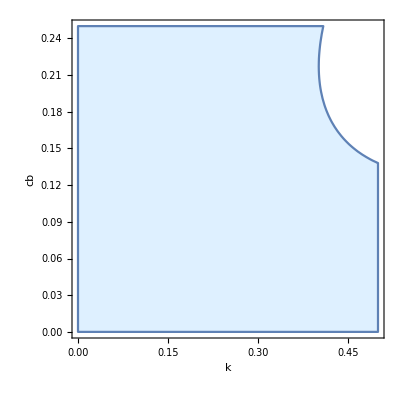

```mathematica
a=0.8;
θ=0.5;
ρ=0.5;
σ=0.3;
RegionPlot[{1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2)>0},{k,0,0.5},{cb,0,0.25},FrameLabel->{k,cb},PlotStyle->LightBlue,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
第一个分析维度：cb\k
```

```mathematica
ClearAll[a,d,ρ,k,θ,cb,σ,A,x,z1,z2,z3]
```

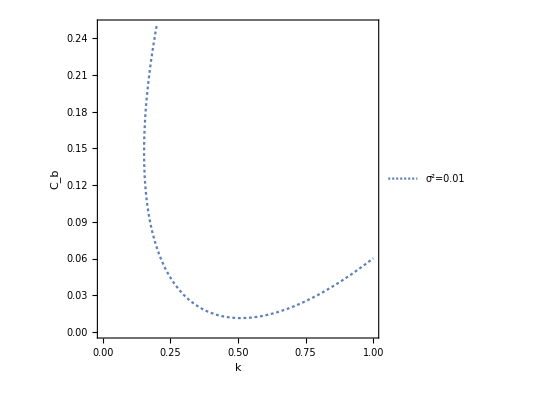

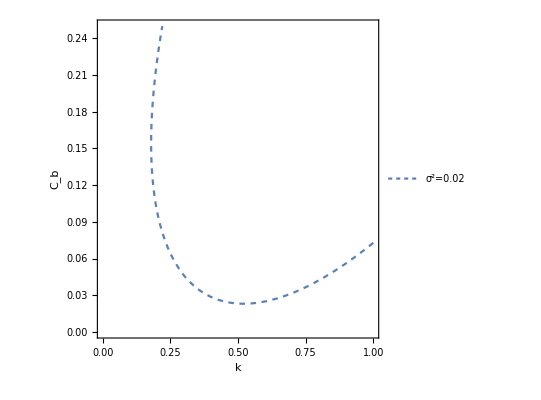

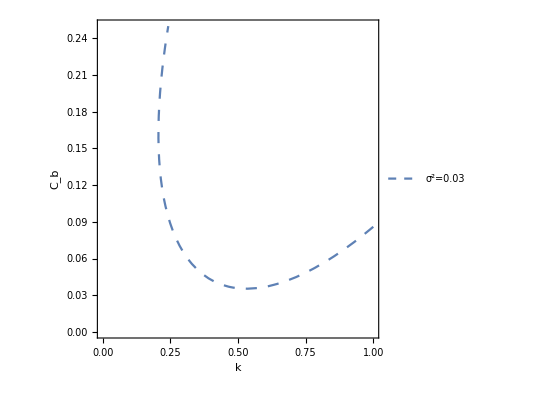

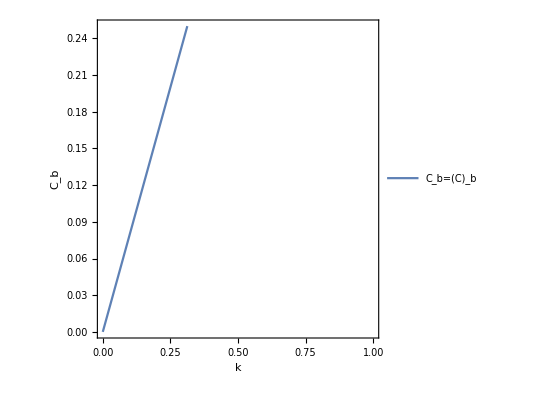

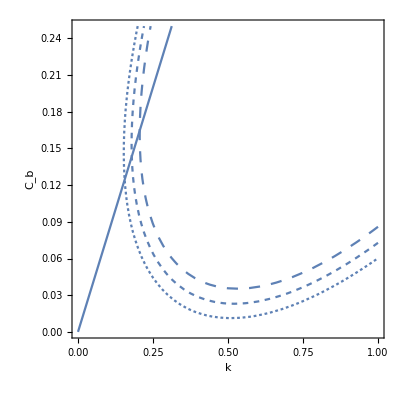

```mathematica
a=0.8;
ρ=0.5;
θ=0.5;
z1=ContourPlot[{{ 1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ))A)/.{A->0.01}}==0},{k,0,1},{cb,0,0.25},FrameLabel->{k,Subscript[C, b]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.005],PlotLegends->Placed[{"σ^2=0.01"},{Left,Center}]]
z2=ContourPlot[{{ 1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A)/.{A->0.02}}==0},{k,0,1},{cb,0,0.25},FrameLabel->{k,Subscript[C, b]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.01],PlotLegends->Placed[{"σ^2=0.02"},{Left,Center}]]
z3=ContourPlot[{{ 1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A)/.{A->0.03}}==0},{k,0,1},{cb,0,0.25},FrameLabel->{k,Subscript[C, b]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.02],PlotLegends->Placed[{"σ^2=0.03"},{Left,Center}]]
x=ContourPlot[{ cb==a k},{k,0,1},{cb,0,0.25},FrameLabel->{k,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"C_b=(C̄)_b"},{Left,Center}]]
Show[z1,z2,z3,x]
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

```mathematica
Manipulate[Plot[1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2),{θ,0,1}],{ρ,0,1},{a,0,1},{k,0,1},{cb,0,0.25},{σ,0,1}]
```

```mathematica
ClearAll[a,d,ρ,A,k,θ,cb,σ,e,g]
```

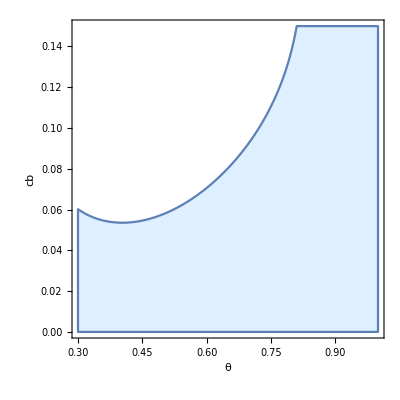

```mathematica
a=0.8;
k=0.4;
ρ=0.5;
σ=0.2;
RegionPlot[{1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2)>0},{θ,0.3,1},{cb,0,0.15},FrameLabel->{θ,cb},PlotStyle->LightBlue,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
第二个分析维度：cb\θ
```

```mathematica
ClearAll[a,ρ,k,θ,cb,A,e,g,e1,e2]
```

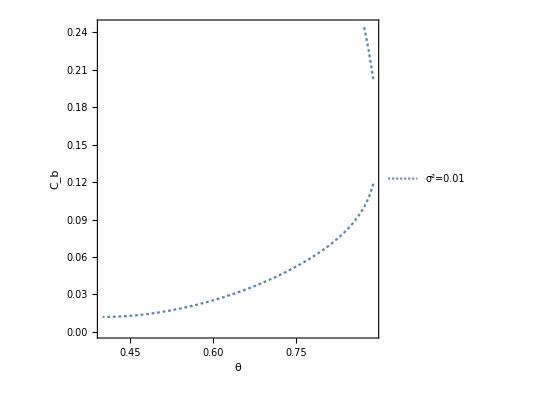

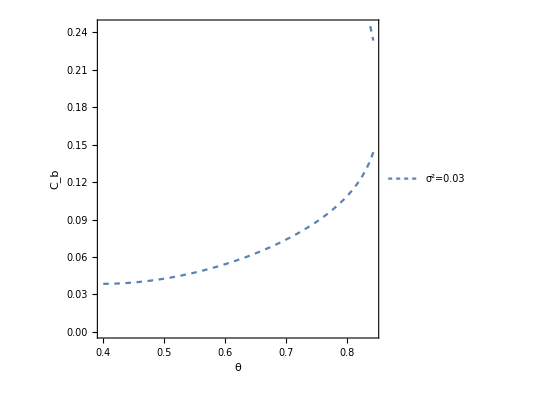

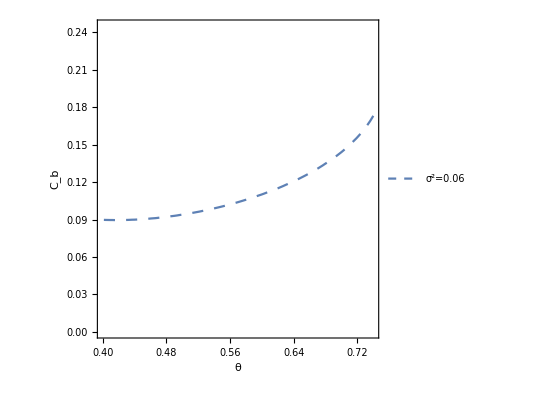

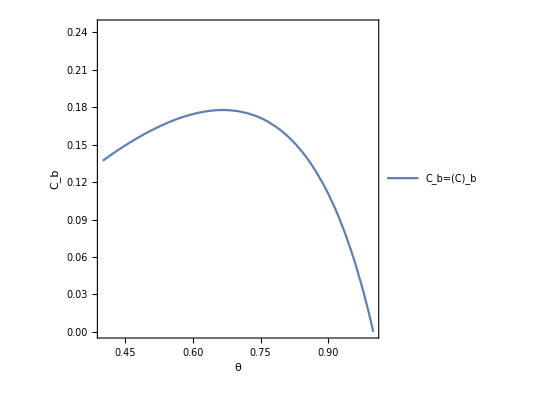

```mathematica
a=0.8;
ρ=0.5;
k=0.4;
e=ContourPlot[{{1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A)/.{A->0.01}}==0},{θ,0.4,0.8888771872666893},{cb,0,0.245},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.005],PlotLegends->Placed[{"σ^2=0.01"},{Left,Center}]]
e1=ContourPlot[{{1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A)/.{A->0.03}}==0},{θ,0.4,0.8428402207570691},{cb,0,0.245},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.01],PlotLegends->Placed[{"σ^2=0.03"},{Left,Center}]]
e2=ContourPlot[{{1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A)/.{A->0.06}}==0},{θ,0.4,0.7398425689043714},{cb,0,0.245},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.02],PlotLegends->Placed[{"σ^2=0.06"},{Left,Center}]]
g=ContourPlot[{ cb==(a (-1+θ) θ)/(-2+θ+θ ρ)},{θ,0.4,1},{cb,0,0.245},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],PlotLegends->Placed[{"C_b=(C̄)_b"},{Left,Center}]]
Show[e,e1,e2,g,PlotRange->{0,0.245}]
```

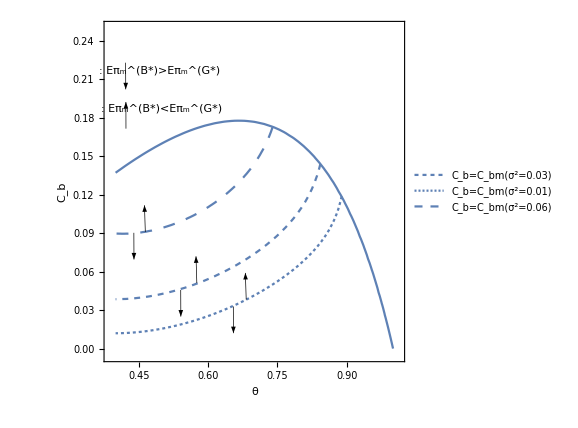

```mathematica
----------------------------------------------------------
```

```mathematica
考虑到惩罚费用反作用的情形（即奖励）
```

```mathematica
ClearAll[a,ρ,k,θ,cb,A,e,g,e1,e2]
```

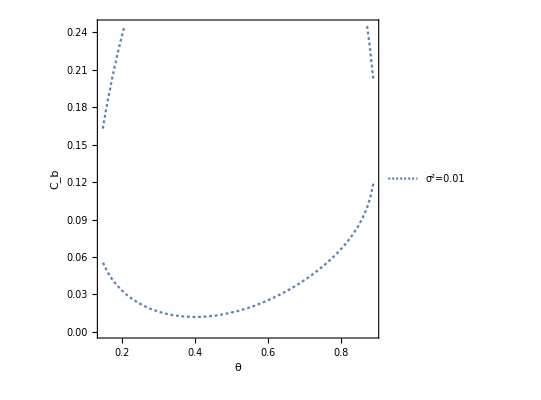

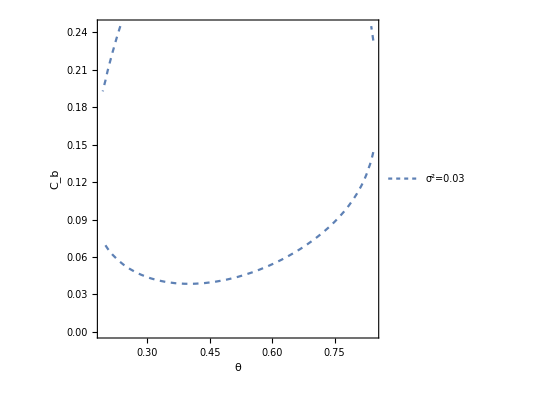

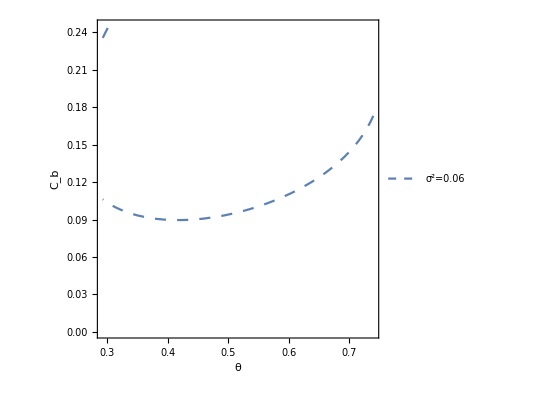

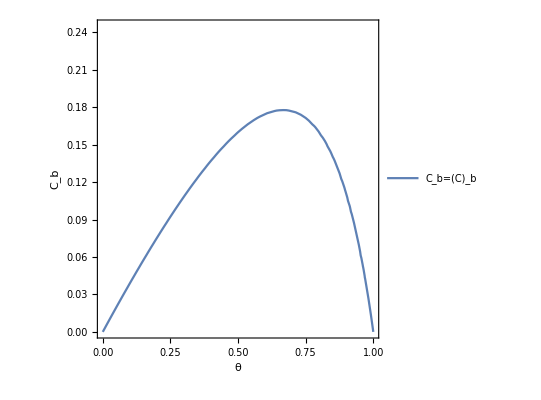

```mathematica
a=0.8;
ρ=0.5;
k=0.4;
e=ContourPlot[{{1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A)/.{A->0.01}}==0},{θ,0.14589321871529717,0.8888771872666893},{cb,0,0.245},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.005],PlotLegends->Placed[{"σ^2=0.01"},{Left,Center}]]
e1=ContourPlot[{{1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A)/.{A->0.03}}==0},{θ,0.1930097009341772,0.8428402207570691},{cb,0,0.245},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.01],PlotLegends->Placed[{"σ^2=0.03"},{Left,Center}]]
e2=ContourPlot[{{1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A)/.{A->0.06}}==0},{θ,0.29303197588503627,0.7398425689043714},{cb,0,0.245},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.02],PlotLegends->Placed[{"σ^2=0.06"},{Left,Center}]]
g=ContourPlot[{ cb==(a (-1+θ) θ)/(-2+θ+θ ρ)},{θ,0,1},{cb,0,0.245},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,20,FontFamily->"Times New Roman"],PlotLegends->Placed[{"C_b=(C̄)_b"},{Left,Center}]]
Show[e,e1,e2,g,PlotRange->{0,0.245}]
```

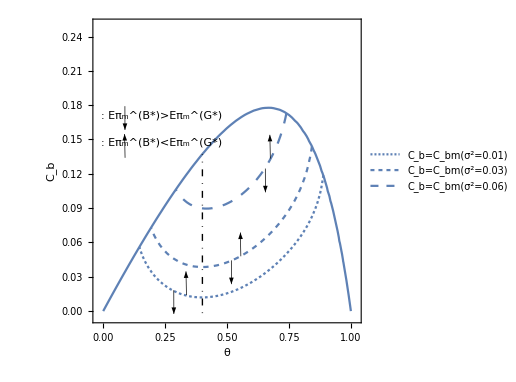

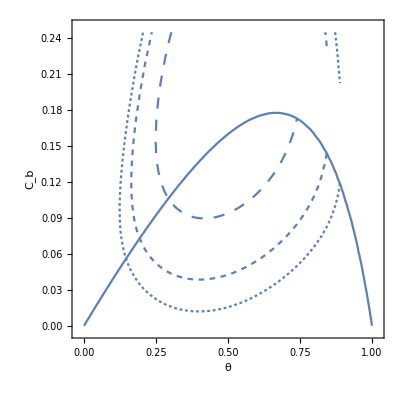

```mathematica
-----------------------------------------------
```

```mathematica
ContourPlot[{{1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A)/.{A->0.03}}==0},{θ,0.4,0.8428402207570691},{cb,0,0.245},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.02],PlotLegends->Placed[{"C_b=C_bm(σ^2=0.06)"},{Left,Center}]]
```

-Graphics-

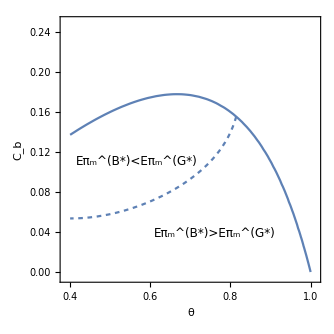

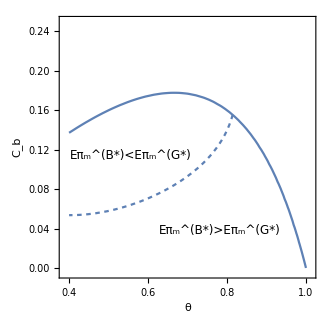

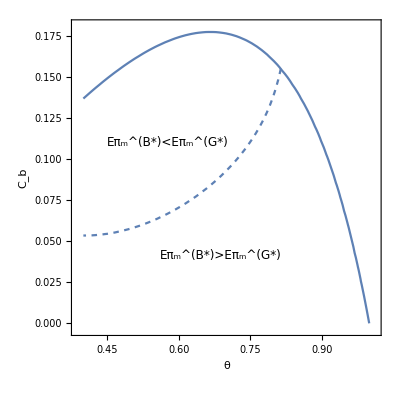

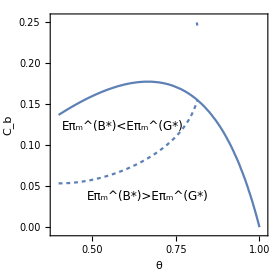

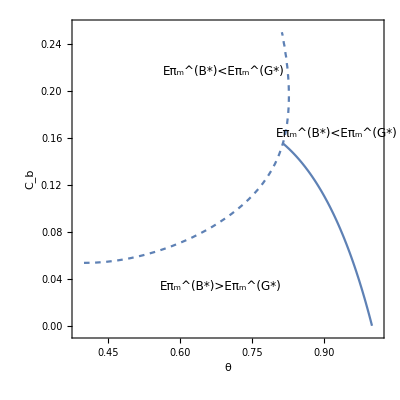

```mathematica
找下交点：
```

```mathematica
FullSimplify[Solve[1/(8 (-4+θ+3 θ ρ))((2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ))/(2 (-1+ρ)+θ (-2+θ+θ ρ))-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2)==0,cb]]
```

{{cb→(4 a θ (1+2 k-ρ) (-1+ρ)+a k θ^5 (1+ρ) (1+3 ρ)+2 a θ^2 (k-2 (1+k) ρ+(2-3 k) ρ^2)+2 a θ^3 (-((-1+ρ) (3+ρ))+3 k (2+ρ+ρ^2))-a θ^4 (2-2 ρ^2+k (7+ρ (14+3 ρ)))-√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (2 (-1+ρ)+k (-4+θ+3 θ ρ))^2-(4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)) (2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ)+(2 (-1+ρ)+θ (-2+θ+θ ρ)) (-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2))))/((2 (-1+ρ)+θ (-2+θ+θ ρ)) (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))},{cb→(4 a θ (1+2 k-ρ) (-1+ρ)+a k θ^5 (1+ρ) (1+3 ρ)+2 a θ^2 (k-2 (1+k) ρ+(2-3 k) ρ^2)+2 a θ^3 (-((-1+ρ) (3+ρ))+3 k (2+ρ+ρ^2))-a θ^4 (2-2 ρ^2+k (7+ρ (14+3 ρ)))+√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (2 (-1+ρ)+k (-4+θ+3 θ ρ))^2-(4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)) (2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ)+(2 (-1+ρ)+θ (-2+θ+θ ρ)) (-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) σ^2))))/((2 (-1+ρ)+θ (-2+θ+θ ρ)) (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))}}

```mathematica
ClearAll[a,d,ρ,k,A,θ,cb,σ,e,g]
```

```mathematica
a=0.8;
ρ=0.5;
k=0.4;
A=0.01;
FullSimplify[Solve[((4 a θ (1+2 k-ρ) (-1+ρ)+a k θ^5 (1+ρ) (1+3 ρ)+2 a θ^2 (k-2 (1+k) ρ+(2-3 k) ρ^2)+2 a θ^3 (-((-1+ρ) (3+ρ))+3 k (2+ρ+ρ^2))-a θ^4 (2-2 ρ^2+k (7+ρ (14+3 ρ)))+√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (2 (-1+ρ)+k (-4+θ+3 θ ρ))^2-(4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)) (2 a^2 (k-θ)^2 (-1+ρ) (-4+θ+3 θ ρ)+(2 (-1+ρ)+θ (-2+θ+θ ρ)) (-4-2 θ+6 θ ρ+k^2 (-4+θ+3 θ ρ)) A))))/((2 (-1+ρ)+θ (-2+θ+θ ρ)) (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2))))-((a (-1+θ) θ)/(-2+θ+θ ρ))==0,θ]]
```

{{θ→-0.940849},{θ→0.},{θ→0.145893},{θ→0.888877},{θ→1.},{θ→1.37534-0.661935 ⅈ},{θ→1.37534+0.661935 ⅈ},{θ→1.47049},{θ→1.81825}}

```mathematica
(a (-1+θ) θ)/(-2+θ+θ ρ)/.{a->0.8,ρ->0.5,θ->0.814439300804185}
```

0.155333

```mathematica
零售商L期望利润：   模型B(此时品牌商知道信息cg内生)-模型G
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

```mathematica
FullSimplify[(-2 a cb (-1+θ) θ (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))+(-1+θ) θ (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) (a^2+σ^2))/(16 (-1+θ) θ (-4+θ+3 θ ρ)^2)-(1/(16 (-4+θ+3 θ ρ)^2)((a^2 (k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2+4 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) σ^2))]
```

1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) σ^2)

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg]
```

```mathematica
Manipulate[Plot[1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) σ^2),{cb,0,0.15}],{ρ,0,1},{a,0,1},{k,0,1},{σ,0,1},{θ,0,1}]
```

```mathematica
ClearAll[a,d,ρ,k,θ,cb,σ]
```

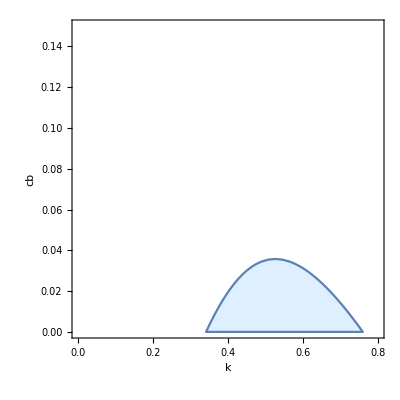

```mathematica
a=0.8;
ρ=0.4;
θ=0.8;
σ=0.1;
RegionPlot[{1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) σ^2)>0},{k,0,0.8},{cb,0,0.15},FrameLabel->{k,cb},PlotStyle->LightBlue,LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"]]
```

```mathematica
第一个分析维度：cb\k
```

```mathematica
ClearAll[a,d,ρ,k,θ,cb,σ,z,x]
```

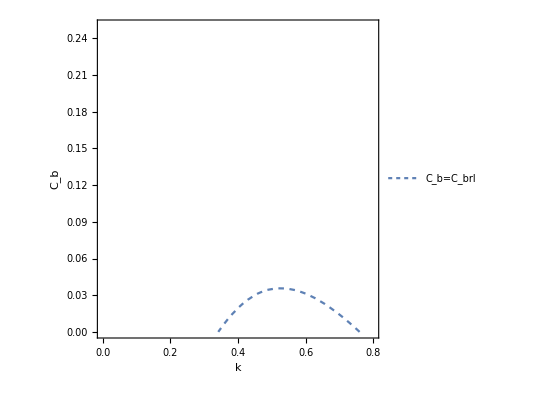

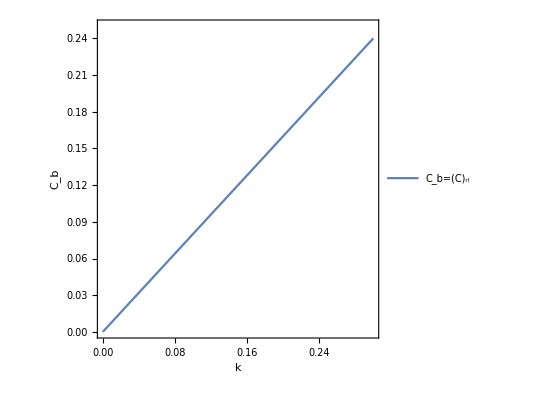

```mathematica
a=0.8;
ρ=0.4;
θ=0.8;
σ=0.1;
z=ContourPlot[{ 1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) σ^2)==0},{k,0,0.8},{cb,0,0.25},FrameLabel->{k,Subscript[C, b]},LabelStyle->Directive[Black,16,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.01],PlotLegends->Placed[{"C_b=C_brl"},{Left,Center}]]
x=ContourPlot[{ cb==a k},{k,0,0.3},{cb,0,0.25},FrameLabel->{k,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"C_b=(C̄)_rl"},{Left,Center}]]
Show[z,x]
```

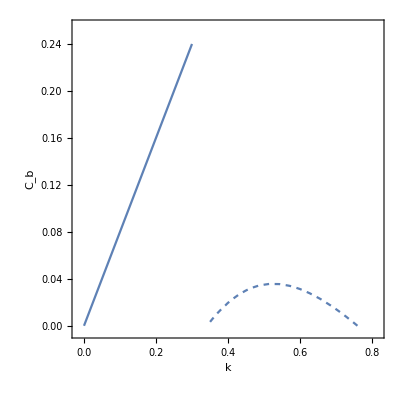

```mathematica
第二个分析维度：cb\θ
```

```mathematica
ClearAll[a,d,ρ,k,A,θ,cb,σ,e5,e3,e4,g1]
```

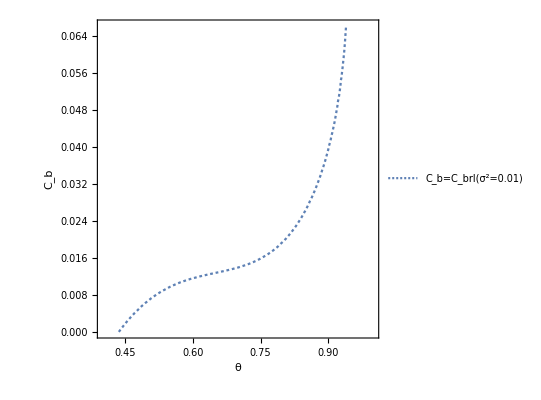

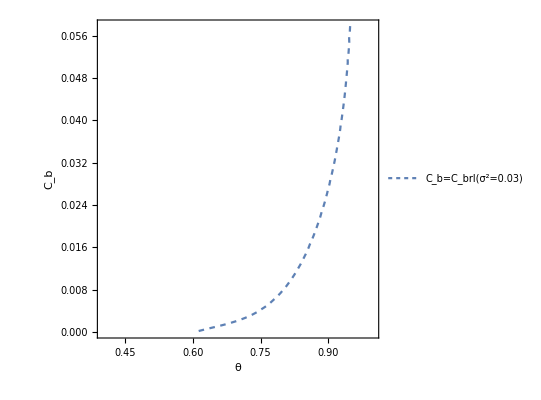

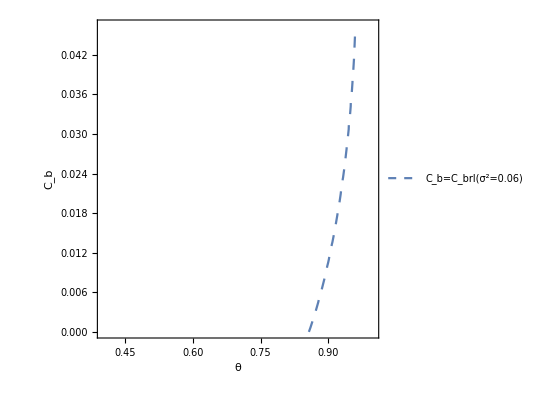

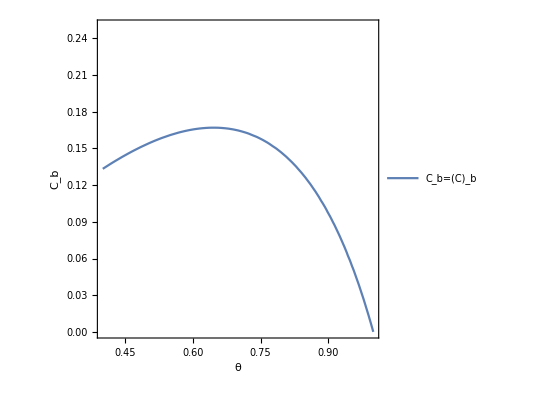

```mathematica
a=0.8;
ρ=0.4;
k=0.4;
e3=ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.01}}==0},{θ,0.4,1},{cb,0,0.06608831371012944},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.005],PlotLegends->Placed[{"C_b=C_brl(σ^2=0.01)"},{Left,Center}]]
e4=ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.03}}==0},{θ,0.4,1},{cb,0,0.057828760636869335},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.01],PlotLegends->Placed[{"C_b=C_brl(σ^2=0.03)"},{Left,Center}]]
e5=ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.06}}==0},{θ,0.4,1},{cb,0,0.04635842752171813},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.02],PlotLegends->Placed[{"C_b=C_brl(σ^2=0.06)"},{Left,Center}]]
g1=ContourPlot[{ cb==(a (-1+θ) θ)/(-2+θ+θ ρ)},{θ,0.4,1},{cb,0,0.25},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"C_b=(C̄)_b"},{Left,Center}]]
Show[e3,e4,e5,g1,PlotRange->{0,0.25}]
```

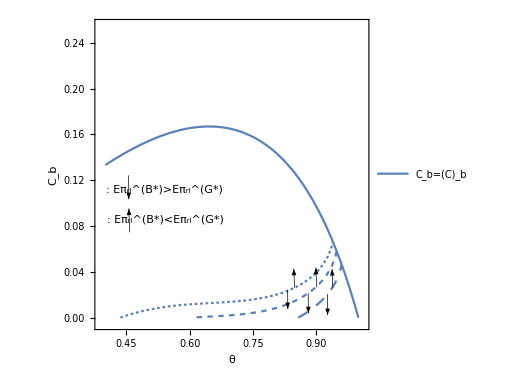

```mathematica
考虑到惩罚费用反作用的情形（即奖励）
```

```mathematica
-------------------------------------------------------
```

```mathematica
ClearAll[a,d,ρ,k,A,θ,cb,σ,e5,e3,e4,g1]
```

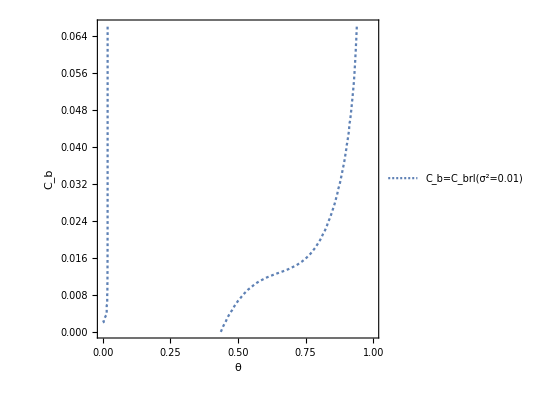

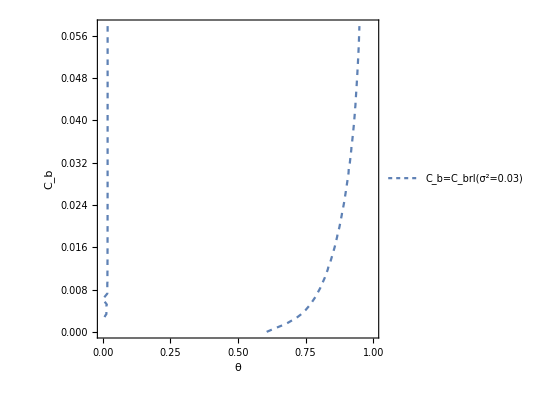

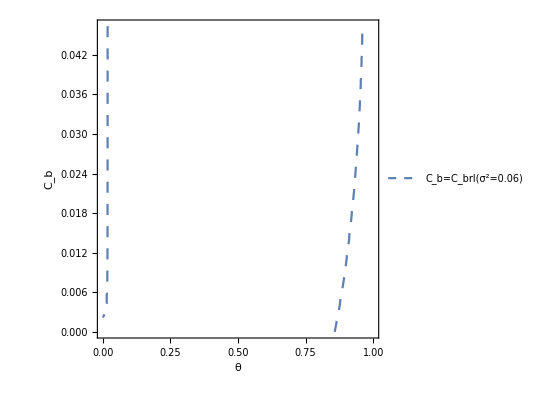

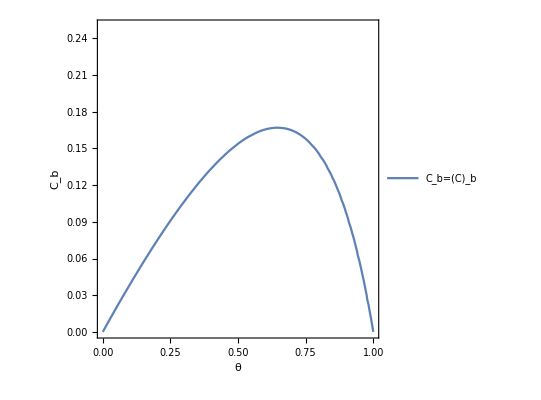

```mathematica
a=0.8;
ρ=0.4;
k=0.4;
e3=ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.01}}==0},{θ,0,1},{cb,0,0.06608831371012944},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.005],PlotLegends->Placed[{"C_b=C_brl(σ^2=0.01)"},{Left,Center}]]
e4=ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.03}}==0},{θ,0,1},{cb,0,0.057828760636869335},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.01],PlotLegends->Placed[{"C_b=C_brl(σ^2=0.03)"},{Left,Center}]]
e5=ContourPlot[{{1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.06}}==0},{θ,0,1},{cb,0,0.04635842752171813},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],ContourStyle->Dashing[0.02],PlotLegends->Placed[{"C_b=C_brl(σ^2=0.06)"},{Left,Center}]]
g1=ContourPlot[{ cb==(a (-1+θ) θ)/(-2+θ+θ ρ)},{θ,0,1},{cb,0,0.25},FrameLabel->{θ,Subscript[C, b]},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"C_b=(C̄)_b"},{Left,Center}]]
Show[e3,e4,e5,g1,PlotRange->{0,0.25}]
```

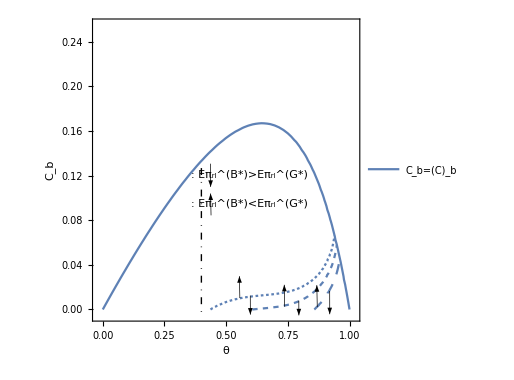

```mathematica
----------------------------------------------------------------
```

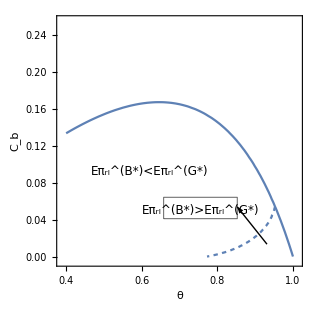

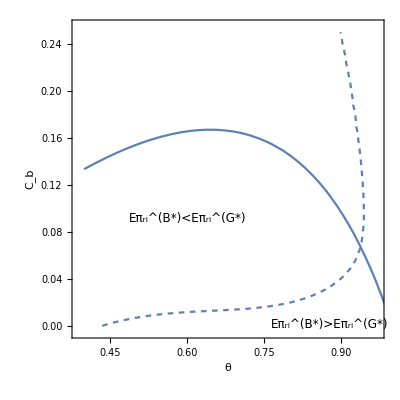

```mathematica
求交点：
```

```mathematica
ClearAll[a,ρ,k,θ,cb,σ,e,g]
```

```mathematica
FullSimplify[Solve[1/(16 (-4+θ+3 θ ρ)^2)(-2 a cb (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)+(cb^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/((-1+θ) θ)-(4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ)))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2-3 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) σ^2)==0,cb]]
```

{{cb→(-32 a θ (1+2 k-ρ) (-1+ρ)^2+a k θ^8 (1+ρ)^2 (1+3 ρ)^2+16 a θ^2 (-1+ρ) (-((-1+ρ) (1+ρ)^2)+k (2+6 ρ^2))-a θ^7 (1+ρ) (-4 (-1+ρ) (1+ρ)^2+k (1+3 ρ) (13+3 ρ (8+ρ)))-4 a θ^3 (-4 (5-8 ρ+2 ρ^3+ρ^4)+k (-39+ρ (2+3 ρ) (6+ρ (2+3 ρ))))+4 a θ^4 (-4 (-1+ρ) ρ (2+ρ (5+ρ))+k (-1+3 ρ) (1+ρ (25+ρ (11+3 ρ))))-4 a θ^5 (-2 (-1+ρ) (1+ρ) (7+ρ (3+2 ρ))+k (26+ρ (46+ρ (31+48 ρ+9 ρ^2))))+4 a θ^6 (-((-1+ρ) (1+ρ)^2 (7+ρ))+k (15+ρ (57+ρ (58+3 ρ (7+3 ρ)))))+√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)^2+(16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)) (4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ))))+3 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) σ^2))))/((2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))},{cb→-((32 a θ (1+2 k-ρ) (-1+ρ)^2-a k θ^8 (1+ρ)^2 (1+3 ρ)^2-16 a θ^2 (-1+ρ) (-((-1+ρ) (1+ρ)^2)+k (2+6 ρ^2))+a θ^7 (1+ρ) (-4 (-1+ρ) (1+ρ)^2+k (1+3 ρ) (13+3 ρ (8+ρ)))+4 a θ^3 (-4 (5-8 ρ+2 ρ^3+ρ^4)+k (-39+ρ (2+3 ρ) (6+ρ (2+3 ρ))))-4 a θ^4 (-4 (-1+ρ) ρ (2+ρ (5+ρ))+k (-1+3 ρ) (1+ρ (25+ρ (11+3 ρ))))+4 a θ^5 (-2 (-1+ρ) (1+ρ) (7+ρ (3+2 ρ))+k (26+ρ (46+ρ (31+48 ρ+9 ρ^2))))-4 a θ^6 (-((-1+ρ) (1+ρ)^2 (7+ρ))+k (15+ρ (57+ρ (58+3 ρ (7+3 ρ)))))+√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)^2+(16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)) (4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ))))+3 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) σ^2))))/((2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))))}}

```mathematica
ClearAll[a,d,ρ,k,θ,cb,σ,e,g]
```

```mathematica
a=0.8;
ρ=0.5;
k=0.4;
A=0.06;
FullSimplify[Solve[((-32 a θ (1+2 k-ρ) (-1+ρ)^2+a k θ^8 (1+ρ)^2 (1+3 ρ)^2+16 a θ^2 (-1+ρ) (-((-1+ρ) (1+ρ)^2)+k (2+6 ρ^2))-a θ^7 (1+ρ) (-4 (-1+ρ) (1+ρ)^2+k (1+3 ρ) (13+3 ρ (8+ρ)))-4 a θ^3 (-4 (5-8 ρ+2 ρ^3+ρ^4)+k (-39+ρ (2+3 ρ) (6+ρ (2+3 ρ))))+4 a θ^4 (-4 (-1+ρ) ρ (2+ρ (5+ρ))+k (-1+3 ρ) (1+ρ (25+ρ (11+3 ρ))))-4 a θ^5 (-2 (-1+ρ) (1+ρ) (7+ρ (3+2 ρ))+k (26+ρ (46+ρ (31+48 ρ+9 ρ^2))))+4 a θ^6 (-((-1+ρ) (1+ρ)^2 (7+ρ))+k (15+ρ (57+ρ (58+3 ρ (7+3 ρ)))))+√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)^2+(16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)) (4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ))))+3 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A))))/((2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))))-((a (-1+θ) θ)/(-2+θ+θ ρ))==0,θ]]
```

{{θ→-0.387426},{θ→-0.387426},{θ→0.},{θ→0.227361-0.431369 ⅈ},{θ→0.227361+0.431369 ⅈ},{θ→0.96651-2.05844 ⅈ},{θ→0.96651+2.05844 ⅈ},{θ→0.967081},{θ→1.},{θ→1.4648},{θ→1.65628},{θ→1.68469},{θ→1.72067},{θ→1.72085},{θ→2.}}

```mathematica
(-32 a θ (1+2 k-ρ) (-1+ρ)^2+a k θ^8 (1+ρ)^2 (1+3 ρ)^2+16 a θ^2 (-1+ρ) (-((-1+ρ) (1+ρ)^2)+k (2+6 ρ^2))-a θ^7 (1+ρ) (-4 (-1+ρ) (1+ρ)^2+k (1+3 ρ) (13+3 ρ (8+ρ)))-4 a θ^3 (-4 (5-8 ρ+2 ρ^3+ρ^4)+k (-39+ρ (2+3 ρ) (6+ρ (2+3 ρ))))+4 a θ^4 (-4 (-1+ρ) ρ (2+ρ (5+ρ))+k (-1+3 ρ) (1+ρ (25+ρ (11+3 ρ))))-4 a θ^5 (-2 (-1+ρ) (1+ρ) (7+ρ (3+2 ρ))+k (26+ρ (46+ρ (31+48 ρ+9 ρ^2))))+4 a θ^6 (-((-1+ρ) (1+ρ)^2 (7+ρ))+k (15+ρ (57+ρ (58+3 ρ (7+3 ρ)))))+√((-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (a^2 (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (4 (-1+ρ) (-2+θ+θ ρ)+k (-4+θ+3 θ ρ)^2)^2+(16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)) (4 a^2 (k-θ) (-1+ρ) (-4+θ+3 θ ρ) (-θ (8-8 ρ+θ (3+θ (-11+3 θ)+2 ρ+5 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (3 (-1+ρ)+θ (-3+θ (2+ρ))))+3 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A))))/((2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2)))/.{θ->0.9670809234780203,a->0.8,ρ->0.5,k->0.4,A->0.06}
```

0.0463584

```mathematica
零售商H利润：
```

```mathematica
模型B（品牌商知道信息Cg内生）-模型G
```

```mathematica
ClearAll[a,d,ρ,k,θ,cb,σ]
```

```mathematica
FullSimplify[(((-1+θ ρ) ((2 a (-1+θ)+cb (-1+ρ))^2+4 (-1+θ)^2 σ^2))/(4 (-1+θ) (-4+θ+3 θ ρ)^2))-(((-1+θ) (-1+θ ρ) (a^2+4 σ^2))/(-4+θ+3 θ ρ)^2)]
```

((-1+θ ρ) (cb (4 a (-1+θ)+cb (-1+ρ)) (-1+ρ)-12 (-1+θ)^2 σ^2))/(4 (-1+θ) (-4+θ+3 θ ρ)^2)

```mathematica
------------------------------------------------------------
```

```mathematica
模型G
模型B（品牌商知道信息Cg外生）
```

```mathematica
品牌商期望利润随k的变化情况，当σ.b2取值不同时
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

0.0179021 (4.+0.5 (2.+5.5 k+3.4375 k^2))

-0.0454545 (-0.019375-0.08 (-1.-2.75 k)-0.615385 (-0.6875-2.2 (-0.5+k)+0.74 (4.+0.5 (2.+5.5 k+3.4375 k^2))))

-0.0454545 (-0.019375-0.08 (-1.-2.75 k)-0.615385 (-0.6875-2.2 (-0.5+k)+0.84 (4.+0.5 (2.+5.5 k+3.4375 k^2))))

-0.0454545 (-0.019375-0.08 (-1.-2.75 k)-0.615385 (-0.6875-2.2 (-0.5+k)+0.94 (4.+0.5 (2.+5.5 k+3.4375 k^2))))

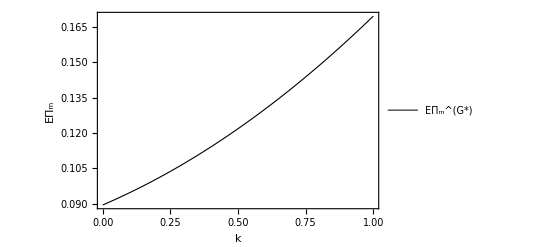

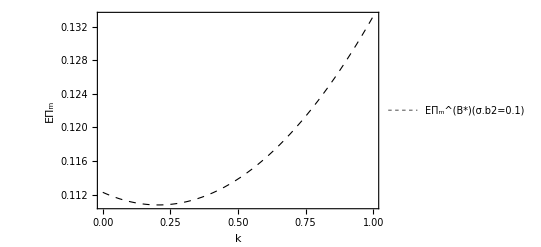

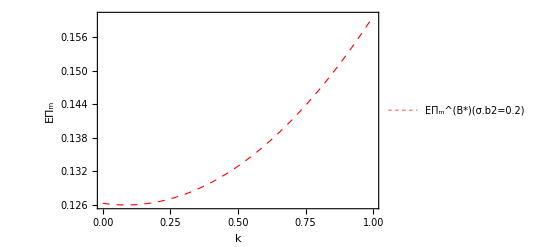

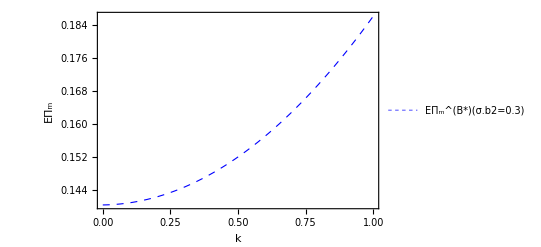

```mathematica
a=0.8;
θ=0.5;
ρ=0.5;
cb=0.05;
cg=0.25;
rG12=(a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))))/(8 (-4+θ+3 θ ρ) (2 (-1+ρ)+θ (-2+θ+θ ρ)))
rB12=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{A->0.1}
rB22=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{A->0.2}
rB32=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{A->0.3}
ar12=Plot[{rG12},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_m"},PlotStyle->{Thickness[0.002],Black},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(G*)"},Right]]
br22=Plot[{rB12},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_m"},PlotStyle->{Thickness[0.002],Black,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(σ.b2=0.1)"},Right]]
dr22=Plot[{rB22},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_m"},PlotStyle->{Thickness[0.002],Red,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(σ.b2=0.2)"},Right]]
fr22=Plot[{rB32},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_m"},PlotStyle->{Thickness[0.002],Blue,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(σ.b2=0.3)"},Right]]
Show[ar12,br22,dr22,fr22,PlotRange->All,Axes->False]
```

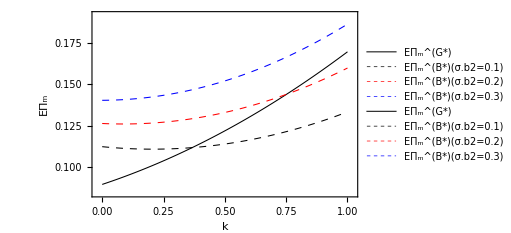

```mathematica
模型G
模型B（品牌商知道信息Cg外生）
```

```mathematica
品牌商期望利润随θ的变化情况，当σ.b2取值不同时
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

(0.08 (4.+θ (15.-8 θ+4. (-2+θ) (1+θ)-1. (-4+2.5 θ)+0.25 (-2+1.5 θ) (-4+2.5 θ))))/((-4+2.5 θ) (-1.+θ (-2+1.5 θ)))

1/(8 (-4+2.5 θ))(-0.08 (-1.+0.5 (-4+2.5 θ))+(0.0025 (2.+θ (2.5+(-5+θ) θ+1.5 (-1+θ) θ)))/((-1+θ) θ)+1/(-1.+θ (-2+1.5 θ))(0.25 (-4+2.5 θ)+0.8 (0.5-θ) (-4+2.5 θ)+0.74 (4.+θ (15.-8 θ+4. (-2+θ) (1+θ)-1. (-4+2.5 θ)+0.25 (-2+1.5 θ) (-4+2.5 θ)))))

1/(8 (-4+2.5 θ))(-0.08 (-1.+0.5 (-4+2.5 θ))+(0.0025 (2.+θ (2.5+(-5+θ) θ+1.5 (-1+θ) θ)))/((-1+θ) θ)+1/(-1.+θ (-2+1.5 θ))(0.25 (-4+2.5 θ)+0.8 (0.5-θ) (-4+2.5 θ)+0.84 (4.+θ (15.-8 θ+4. (-2+θ) (1+θ)-1. (-4+2.5 θ)+0.25 (-2+1.5 θ) (-4+2.5 θ)))))

1/(8 (-4+2.5 θ))(-0.08 (-1.+0.5 (-4+2.5 θ))+(0.0025 (2.+θ (2.5+(-5+θ) θ+1.5 (-1+θ) θ)))/((-1+θ) θ)+1/(-1.+θ (-2+1.5 θ))(0.25 (-4+2.5 θ)+0.8 (0.5-θ) (-4+2.5 θ)+0.94 (4.+θ (15.-8 θ+4. (-2+θ) (1+θ)-1. (-4+2.5 θ)+0.25 (-2+1.5 θ) (-4+2.5 θ)))))

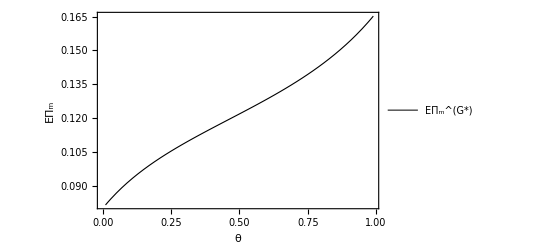

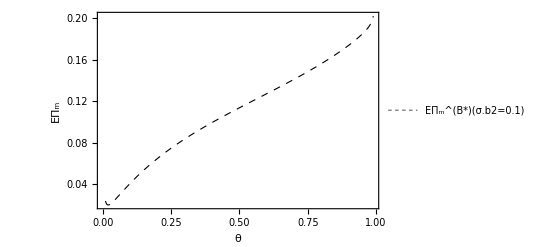

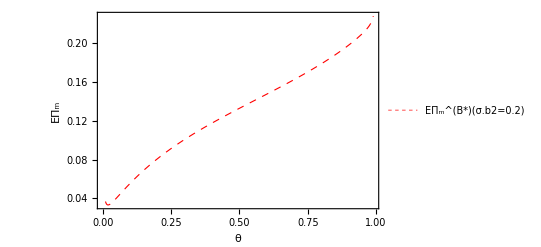

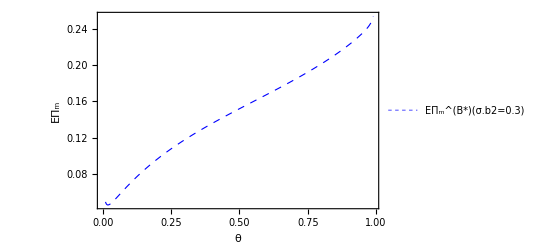

```mathematica
a=0.8;
k=0.5;
ρ=0.5;
cb=0.05;
cg=0.25;
rG12=(a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))))/(8 (-4+θ+3 θ ρ) (2 (-1+ρ)+θ (-2+θ+θ ρ)))
rB12=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{A->0.1}
rB22=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{A->0.2}
rB32=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{A->0.3}
ar12=Plot[{rG12},{θ,0.01,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_m"},PlotStyle->{Thickness[0.002],Black},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(G*)"},Right]]
br22=Plot[{rB12},{θ,0.01,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_m"},PlotStyle->{Thickness[0.002],Black,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(σ.b2=0.1)"},Right]]
dr22=Plot[{rB22},{θ,0.01,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_m"},PlotStyle->{Thickness[0.002],Red,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(σ.b2=0.2)"},Right]]
fr22=Plot[{rB32},{θ,0.01,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_m"},PlotStyle->{Thickness[0.002],Blue,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(σ.b2=0.3)"},Right]]
Show[ar12,br22,dr22,fr22,PlotRange->All,Axes->False]
```

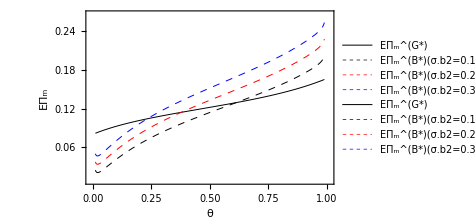

```mathematica
-----------------------------------------------------
```

```mathematica
Revision---2
```

```mathematica
模型G
模型B（品牌商知道信息Cg外生）
```

```mathematica
品牌商期望利润随θ的变化情况，当σ.b2取值不同时
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A,rG12,rB12,rB22,rB32,ar12,br22,dr22,fr22]
```

(0.08 (4.+θ (15.-8 θ+4. (-2+θ) (1+θ)-0.8 (-4+2.5 θ)+0.16 (-2+1.5 θ) (-4+2.5 θ))))/((-4+2.5 θ) (-1.+θ (-2+1.5 θ)))

1/(8 (-4+2.5 θ))(-0.08 (-1.+0.4 (-4+2.5 θ))+(0.0025 (2.+θ (2.5+(-5+θ) θ+1.5 (-1+θ) θ)))/((-1+θ) θ)+1/(-1.+θ (-2+1.5 θ))(0.25 (-4+2.5 θ)+0.8 (0.4-θ) (-4+2.5 θ)+0.74 (4.+θ (15.-8 θ+4. (-2+θ) (1+θ)-0.8 (-4+2.5 θ)+0.16 (-2+1.5 θ) (-4+2.5 θ)))))

1/(8 (-4+2.5 θ))(-0.08 (-1.+0.4 (-4+2.5 θ))+(0.0025 (2.+θ (2.5+(-5+θ) θ+1.5 (-1+θ) θ)))/((-1+θ) θ)+1/(-1.+θ (-2+1.5 θ))(0.25 (-4+2.5 θ)+0.8 (0.4-θ) (-4+2.5 θ)+0.84 (4.+θ (15.-8 θ+4. (-2+θ) (1+θ)-0.8 (-4+2.5 θ)+0.16 (-2+1.5 θ) (-4+2.5 θ)))))

1/(8 (-4+2.5 θ))(-0.08 (-1.+0.4 (-4+2.5 θ))+(0.0025 (2.+θ (2.5+(-5+θ) θ+1.5 (-1+θ) θ)))/((-1+θ) θ)+1/(-1.+θ (-2+1.5 θ))(0.25 (-4+2.5 θ)+0.8 (0.4-θ) (-4+2.5 θ)+0.94 (4.+θ (15.-8 θ+4. (-2+θ) (1+θ)-0.8 (-4+2.5 θ)+0.16 (-2+1.5 θ) (-4+2.5 θ)))))

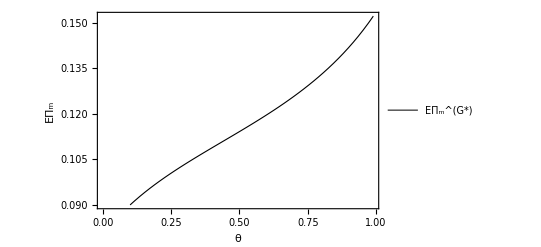

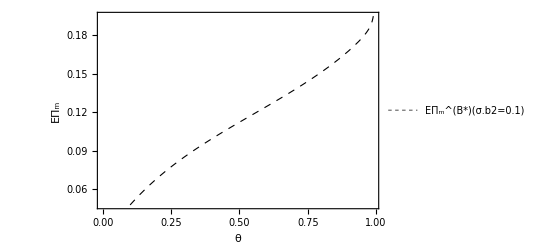

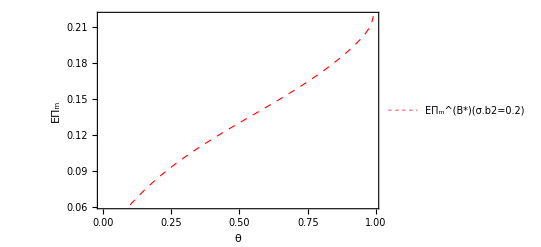

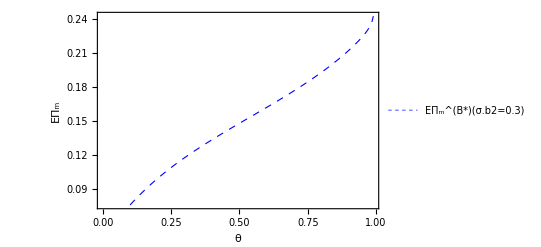

```mathematica
a=0.8;
k=0.4;
ρ=0.5;
cb=0.05;
cg=0.25;
rG12=(a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))))/(8 (-4+θ+3 θ ρ) (2 (-1+ρ)+θ (-2+θ+θ ρ)))
rB12=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{A->0.1}
rB22=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{A->0.2}
rB32=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{A->0.3}
ar12=Plot[{rG12},{θ,0.1,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_m"},PlotStyle->{Thickness[0.002],Black},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(G*)"},Right]]
br22=Plot[{rB12},{θ,0.1,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_m"},PlotStyle->{Thickness[0.002],Black,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(σ.b2=0.1)"},Right]]
dr22=Plot[{rB22},{θ,0.1,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_m"},PlotStyle->{Thickness[0.002],Red,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(σ.b2=0.2)"},Right]]
fr22=Plot[{rB32},{θ,0.1,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_m"},PlotStyle->{Thickness[0.002],Blue,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(σ.b2=0.3)"},Right]]
Show[ar12,br22,dr22,fr22,PlotRange->All,Axes->False]
```

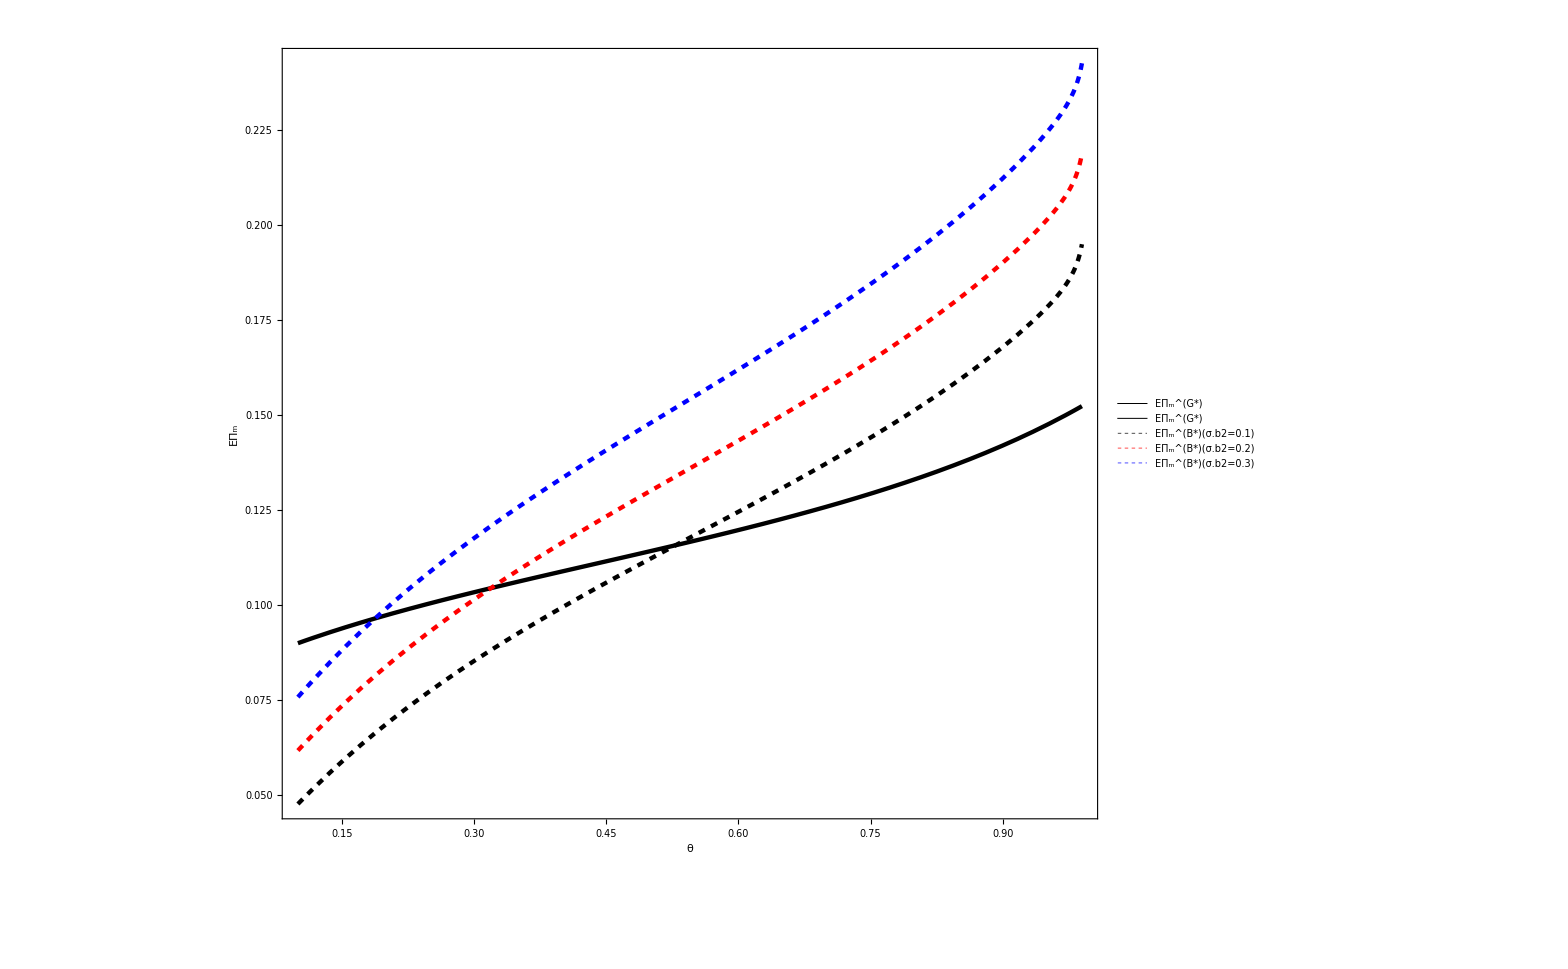

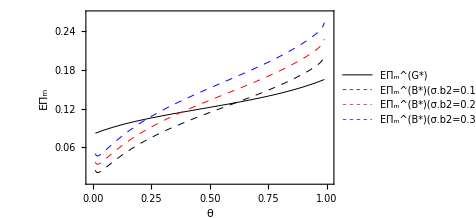

```mathematica
-----------------------------------------------------
```

```mathematica
模型G
模型B（品牌商知道信息Cg外生）
```

```mathematica
零售商L期望利润随k的变化情况，当σ.b2取值不同时
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

0.00826446 (0.4 (0.5+7.5625 k^2)+0.242367 (6.39063-28.1016 k+55.8916 k^2))

-0.0125189 (-0.033111-0.040625 (-3.31875-10.3813 k)-0.25 (2.83594+2.2 (-2.875+8.59375 k)+0.74 (6.39063-28.1016 k+55.8916 k^2)))

0.00826446 (0.8 (0.5+7.5625 k^2)+0.242367 (6.39063-28.1016 k+55.8916 k^2))

-0.0125189 (-0.033111-0.040625 (-3.31875-10.3813 k)-0.25 (2.83594+2.2 (-2.875+8.59375 k)+0.84 (6.39063-28.1016 k+55.8916 k^2)))

0.00826446 (1.6 (0.5+7.5625 k^2)+0.242367 (6.39063-28.1016 k+55.8916 k^2))

-0.0125189 (-0.033111-0.040625 (-3.31875-10.3813 k)-0.25 (2.83594+2.2 (-2.875+8.59375 k)+1.04 (6.39063-28.1016 k+55.8916 k^2)))

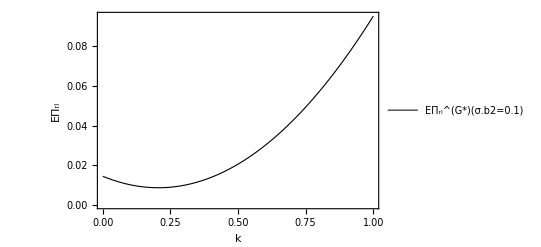

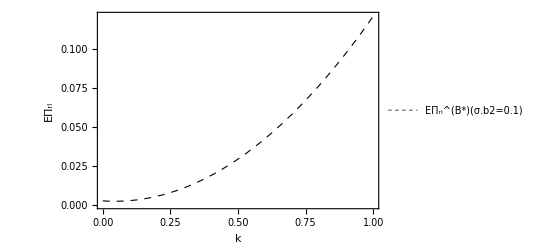

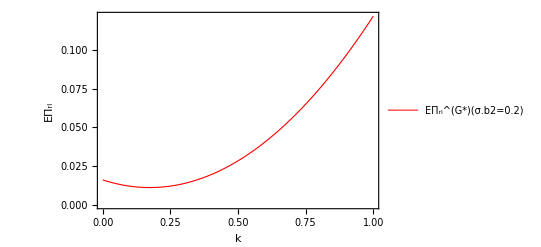

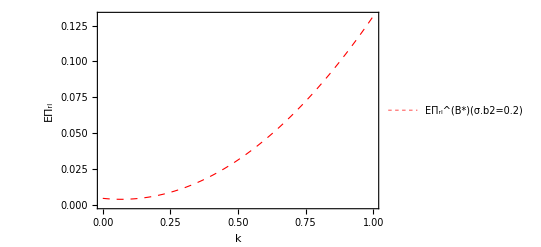

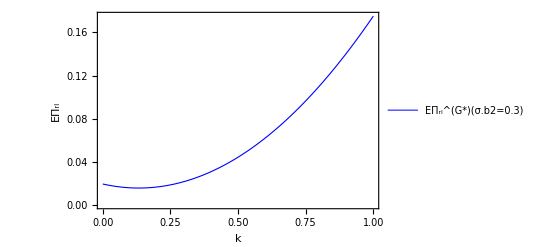

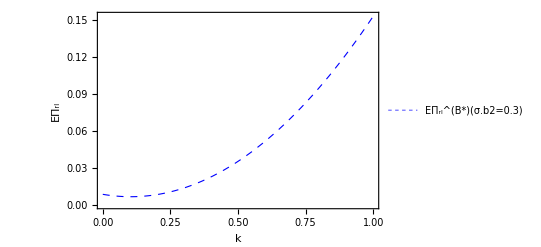

```mathematica
a=0.8;
θ=0.5;
ρ=0.5;
cb=0.05;
cg=0.25;
rG1=1/(16 (-4+θ+3 θ ρ)^2)((a^2 (k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2+4 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.1}
rB1=(cb^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))-2 cb (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)-2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))+a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ))))+(-1+θ) θ (16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))+(k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))) (a^2+A)))/(16 (-1+θ) θ (-4+θ+3 θ ρ)^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{A->0.1}
rG2=1/(16 (-4+θ+3 θ ρ)^2)((a^2 (k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2+4 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.2}
rB2=(cb^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))-2 cb (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)-2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))+a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ))))+(-1+θ) θ (16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))+(k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))) (a^2+A)))/(16 (-1+θ) θ (-4+θ+3 θ ρ)^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{A->0.2}
rG3=1/(16 (-4+θ+3 θ ρ)^2)((a^2 (k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2+4 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.4}
rB3=(cb^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))-2 cb (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)-2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))+a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ))))+(-1+θ) θ (16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))+(k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))) (a^2+A)))/(16 (-1+θ) θ (-4+θ+3 θ ρ)^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{A->0.4}
ar1=Plot[{rG1},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_rl"},PlotStyle->{Thickness[0.002],Black},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(G*)(σ.b2=0.1)"},Right]]
br2=Plot[{rB1},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_rl"},PlotStyle->{Thickness[0.002],Black,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(B*)(σ.b2=0.1)"},Right]]
cr1=Plot[{rG2},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_rl"},PlotStyle->{Thickness[0.002],Red},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(G*)(σ.b2=0.2)"},Right]]
dr2=Plot[{rB2},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_rl"},PlotStyle->{Thickness[0.002],Red,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(B*)(σ.b2=0.2)"},Right]]
er1=Plot[{rG3},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_rl"},PlotStyle->{Thickness[0.002],Blue},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(G*)(σ.b2=0.3)"},Right]]
fr2=Plot[{rB3},{k,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"k","EΠ_rl"},PlotStyle->{Thickness[0.002],Blue,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(B*)(σ.b2=0.3)"},Right]]
Show[ar1,br2,cr1,dr2,er1,fr2,PlotRange->All,Axes->False]
```

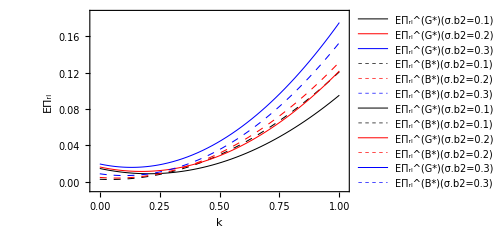

```mathematica
模型G
模型B（品牌商知道信息Cg外生）
```

```mathematica
零售商L期望利润随θ的变化情况，当σ.b2取值不同时
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

1/(16 (-4+2.5 θ)^2)(0.4 (-2. (-1+θ) θ+0.25 (-4+2.5 θ)^2)+1/(-1.+θ (-2+1.5 θ))^2 0.64 (1. θ (-4+2.5 θ) (10.+13. θ-31. θ^2+11.75 θ^3)+0.25 (-4+2.5 θ)^2 (4.+10. θ-4. θ^2-6. θ^3+2.25 θ^4)-2. θ (-1.-19. θ-6. θ^2+72.875 θ^3-64. θ^4+16. θ^5)))

(0.0025 (-8.-4. θ+31.5 θ^2-26.25 θ^3+6.25 θ^4) (-1.+θ (-2+1.5 θ))^2-0.1 (-1+θ) θ (-1.+θ (-2+1.5 θ)) (0.25 θ (-4+2.5 θ)+0.8 (-4.-5. θ+14. θ^2-5.75 θ^3)+0.4 (-4+2.5 θ) (4.+θ (6.-11. θ+3.75 θ^2)))+(-1+θ) θ (-0.5 (-4+2.5 θ)^2 (-0.5+(-1+θ) θ)+0.74 (1. θ (-4+2.5 θ) (10.+13. θ-31. θ^2+11.75 θ^3)+0.25 (-4+2.5 θ)^2 (4.+10. θ-4. θ^2-6. θ^3+2.25 θ^4)-2. θ (-1.-19. θ-6. θ^2+72.875 θ^3-64. θ^4+16. θ^5))-0.8 (-4+2.5 θ) (0.5 (-4+2.5 θ) (-2.+θ (-4+3.5 θ))-2 θ (3.+θ (3.75+2 (-4+θ) θ+2. (-1+θ) θ)))))/(16 (-1+θ) θ (-4+2.5 θ)^2 (-1.+θ (-2+1.5 θ))^2)

1/(16 (-4+2.5 θ)^2)(0.8 (-2. (-1+θ) θ+0.25 (-4+2.5 θ)^2)+1/(-1.+θ (-2+1.5 θ))^2 0.64 (1. θ (-4+2.5 θ) (10.+13. θ-31. θ^2+11.75 θ^3)+0.25 (-4+2.5 θ)^2 (4.+10. θ-4. θ^2-6. θ^3+2.25 θ^4)-2. θ (-1.-19. θ-6. θ^2+72.875 θ^3-64. θ^4+16. θ^5)))

(0.0025 (-8.-4. θ+31.5 θ^2-26.25 θ^3+6.25 θ^4) (-1.+θ (-2+1.5 θ))^2-0.1 (-1+θ) θ (-1.+θ (-2+1.5 θ)) (0.25 θ (-4+2.5 θ)+0.8 (-4.-5. θ+14. θ^2-5.75 θ^3)+0.4 (-4+2.5 θ) (4.+θ (6.-11. θ+3.75 θ^2)))+(-1+θ) θ (-0.5 (-4+2.5 θ)^2 (-0.5+(-1+θ) θ)+0.84 (1. θ (-4+2.5 θ) (10.+13. θ-31. θ^2+11.75 θ^3)+0.25 (-4+2.5 θ)^2 (4.+10. θ-4. θ^2-6. θ^3+2.25 θ^4)-2. θ (-1.-19. θ-6. θ^2+72.875 θ^3-64. θ^4+16. θ^5))-0.8 (-4+2.5 θ) (0.5 (-4+2.5 θ) (-2.+θ (-4+3.5 θ))-2 θ (3.+θ (3.75+2 (-4+θ) θ+2. (-1+θ) θ)))))/(16 (-1+θ) θ (-4+2.5 θ)^2 (-1.+θ (-2+1.5 θ))^2)

1/(16 (-4+2.5 θ)^2)(1.6 (-2. (-1+θ) θ+0.25 (-4+2.5 θ)^2)+1/(-1.+θ (-2+1.5 θ))^2 0.64 (1. θ (-4+2.5 θ) (10.+13. θ-31. θ^2+11.75 θ^3)+0.25 (-4+2.5 θ)^2 (4.+10. θ-4. θ^2-6. θ^3+2.25 θ^4)-2. θ (-1.-19. θ-6. θ^2+72.875 θ^3-64. θ^4+16. θ^5)))

(0.0025 (-8.-4. θ+31.5 θ^2-26.25 θ^3+6.25 θ^4) (-1.+θ (-2+1.5 θ))^2-0.1 (-1+θ) θ (-1.+θ (-2+1.5 θ)) (0.25 θ (-4+2.5 θ)+0.8 (-4.-5. θ+14. θ^2-5.75 θ^3)+0.4 (-4+2.5 θ) (4.+θ (6.-11. θ+3.75 θ^2)))+(-1+θ) θ (-0.5 (-4+2.5 θ)^2 (-0.5+(-1+θ) θ)+1.04 (1. θ (-4+2.5 θ) (10.+13. θ-31. θ^2+11.75 θ^3)+0.25 (-4+2.5 θ)^2 (4.+10. θ-4. θ^2-6. θ^3+2.25 θ^4)-2. θ (-1.-19. θ-6. θ^2+72.875 θ^3-64. θ^4+16. θ^5))-0.8 (-4+2.5 θ) (0.5 (-4+2.5 θ) (-2.+θ (-4+3.5 θ))-2 θ (3.+θ (3.75+2 (-4+θ) θ+2. (-1+θ) θ)))))/(16 (-1+θ) θ (-4+2.5 θ)^2 (-1.+θ (-2+1.5 θ))^2)

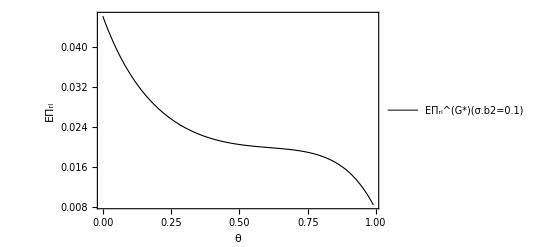

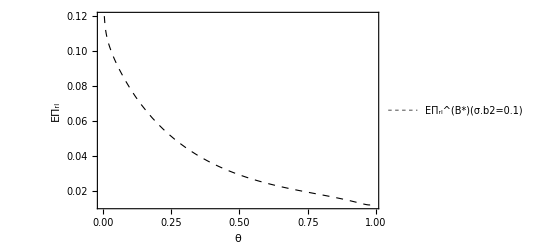

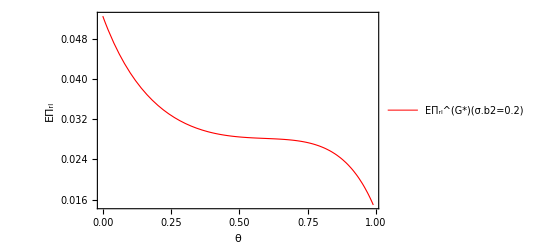

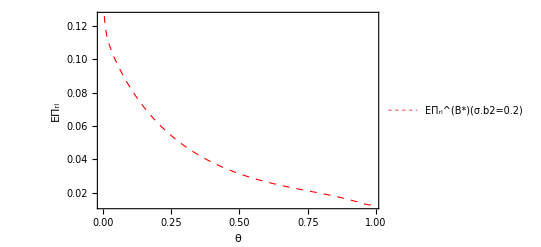

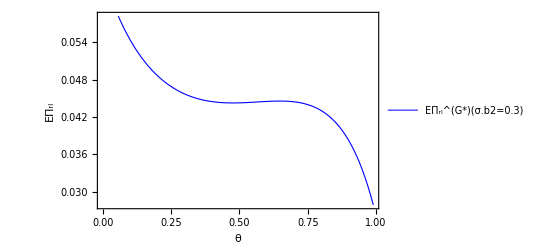

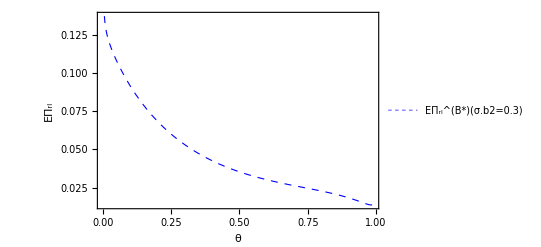

```mathematica
a=0.8;
k=0.5;
ρ=0.5;
cb=0.05;
cg=0.25;
rG1=1/(16 (-4+θ+3 θ ρ)^2)((a^2 (k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2+4 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.1}
rB1=(cb^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))-2 cb (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)-2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))+a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ))))+(-1+θ) θ (16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))+(k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))) (a^2+A)))/(16 (-1+θ) θ (-4+θ+3 θ ρ)^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{A->0.1}
rG2=1/(16 (-4+θ+3 θ ρ)^2)((a^2 (k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2+4 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.2}
rB2=(cb^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))-2 cb (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)-2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))+a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ))))+(-1+θ) θ (16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))+(k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))) (a^2+A)))/(16 (-1+θ) θ (-4+θ+3 θ ρ)^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{A->0.2}
rG3=1/(16 (-4+θ+3 θ ρ)^2)((a^2 (k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))))/(2 (-1+ρ)+θ (-2+θ+θ ρ))^2+4 (4 (-1+θ) θ (-1+ρ)+k^2 (-4+θ+3 θ ρ)^2) A)/.{A->0.4}
rB3=(cb^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2 (16 (-1+ρ)-16 θ ρ^2-3 θ^3 (3+ρ) (1+3 ρ)+θ^4 (1+3 ρ)^2+4 θ^2 (1+ρ) (5+ρ^2))-2 cb (-1+θ) θ (2 (-1+ρ)+θ (-2+θ+θ ρ)) (4 cg θ (-1+ρ)^2 (-4+θ+3 θ ρ)-2 a (-1+ρ) (8 (-1+ρ)+4 θ^2 (3+ρ)+θ^3 (-3+(-6+ρ) ρ)-4 θ (1+ρ^2))+a k (-4+θ+3 θ ρ) (8-8 ρ+θ (8+8 (-1+ρ) ρ+θ^2 (1+ρ) (1+3 ρ)-2 θ (3+5 ρ))))+(-1+θ) θ (16 cg^2 (-1+ρ) (-1+(-1+θ) θ+ρ) (-4+θ+3 θ ρ)^2+8 a cg (-1+ρ) (-4+θ+3 θ ρ) (-2 θ (6-6 ρ+θ (3+2 (-4+θ) θ+4 (-1+θ) θ ρ+3 ρ^2))+k (-4+θ+3 θ ρ) (4 (-1+ρ)+θ (-4+θ (3+ρ))))+(k^2 (-4+θ+3 θ ρ)^2 (-20 θ (-1+ρ)+16 (-1+ρ)^2-4 θ^3 (1+ρ)+θ^4 (1+ρ)^2+4 θ^2 (-2+ρ+2 ρ^2))-4 k θ (-1+ρ) (-4+θ+3 θ ρ) (-20 (-1+ρ)-2 θ^2 (11+9 ρ)+θ^3 (5+3 ρ (4+ρ))+4 θ (3+ρ (-1+3 ρ)))+4 θ (-1+ρ) (-4 (-1+ρ)^2+4 θ (-1+ρ) (9+ρ)+4 θ^5 (1+2 ρ)^2-4 θ^4 (1+2 ρ) (7+2 ρ)+θ^2 (4-40 ρ^2)+θ^3 (51+ρ (35+ρ (13+9 ρ))))) (a^2+A)))/(16 (-1+θ) θ (-4+θ+3 θ ρ)^2 (2 (-1+ρ)+θ (-2+θ+θ ρ))^2)/.{A->0.4}
ar1=Plot[{rG1},{θ,0,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_rl"},PlotStyle->{Thickness[0.002],Black},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(G*)(σ.b2=0.1)"},Right]]
br2=Plot[{rB1},{θ,0,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_rl"},PlotStyle->{Thickness[0.002],Black,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(B*)(σ.b2=0.1)"},Right]]
cr1=Plot[{rG2},{θ,0,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_rl"},PlotStyle->{Thickness[0.002],Red},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(G*)(σ.b2=0.2)"},Right]]
dr2=Plot[{rB2},{θ,0,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_rl"},PlotStyle->{Thickness[0.002],Red,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(B*)(σ.b2=0.2)"},Right]]
er1=Plot[{rG3},{θ,0,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_rl"},PlotStyle->{Thickness[0.002],Blue},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(G*)(σ.b2=0.3)"},Right]]
fr2=Plot[{rB3},{θ,0,0.99},PlotRange->Automatic,Frame->True,FrameLabel->{"θ","EΠ_rl"},PlotStyle->{Thickness[0.002],Blue,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_rl^(B*)(σ.b2=0.3)"},Right]]
Show[ar1,br2,cr1,dr2,er1,fr2,PlotRange->All,Axes->False]
```

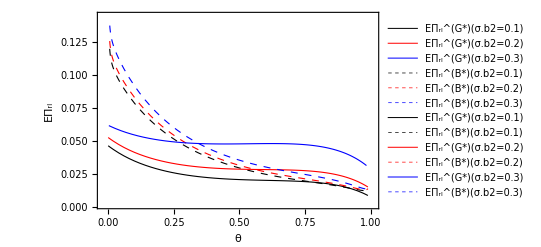

```mathematica
----------------------------------------------------------------
```

```mathematica
模型G
模型B（品牌商知道信息Cg外生）
```

```mathematica
品牌商期望利润随σ.b2的变化情况，当k取值不同时
```

```mathematica
ClearAll[a,d,θ,σ,k,ρ,cb,cg,A]
```

0.0179021 (4.+0.5 (2.+5.5 k+3.4375 k^2))

-0.0454545 (0.082625-0.615385 (3.5795+5.29219 A))

-0.0454545 (0.104625-0.615385 (3.5685+5.61875 A))

-0.0454545 (0.126625-0.615385 (3.5795+5.97969 A))

-Graphics-

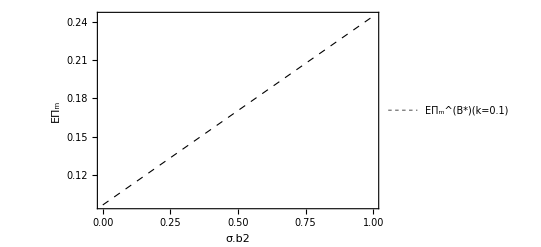

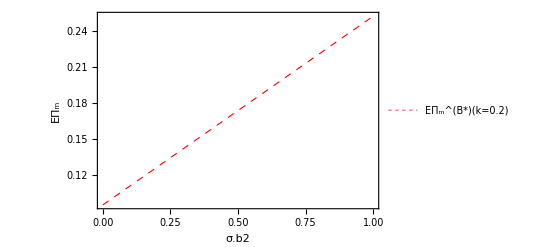

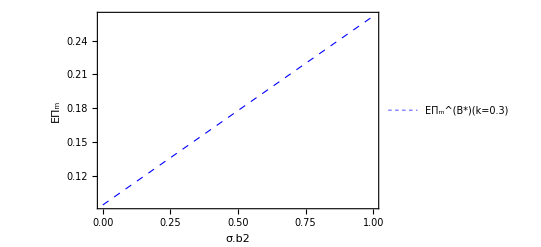

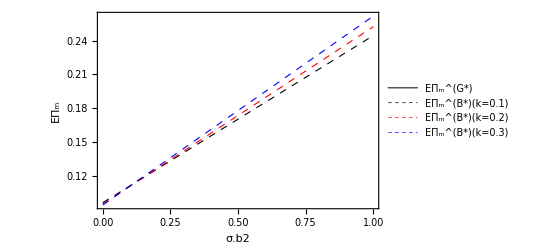

```mathematica
a=0.8;
θ=0.5;
ρ=0.5;
cb=0.05;
cg=0.25;
rG121=(a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))))/(8 (-4+θ+3 θ ρ) (2 (-1+ρ)+θ (-2+θ+θ ρ)))
rB121=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{k->0.1}
rB221=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{k->0.2}
rB321=1/(8 (-4+θ+3 θ ρ))(-2 a cb (2 (-1+ρ)+k (-4+θ+3 θ ρ))+(cb^2 (4-4 ρ+θ (2+(-5+θ) θ+3 (-1+θ) θ ρ+2 ρ^2)))/((-1+θ) θ)+(-8 cg^2 (-1+ρ) (-4+θ+3 θ ρ)-8 a cg (k-θ) (-1+ρ) (-4+θ+3 θ ρ)+a^2 (8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ)))+(8-8 ρ+θ (12-8 θ+8 (-2+θ) (1+θ) ρ+12 ρ^2+4 k (-1+ρ) (-4+θ+3 θ ρ)+k^2 (-2+θ+θ ρ) (-4+θ+3 θ ρ))) A)/(2 (-1+ρ)+θ (-2+θ+θ ρ)))/.{k->0.3}
ar121=Plot[{rG121},{A,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"σ.b2","EΠ_m"},PlotStyle->{Thickness[0.002],Black},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(G*)"},Right]]
br221=Plot[{rB121},{A,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"σ.b2","EΠ_m"},PlotStyle->{Thickness[0.002],Black,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(k=0.1)"},Right]]
dr221=Plot[{rB221},{A,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"σ.b2","EΠ_m"},PlotStyle->{Thickness[0.002],Red,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(k=0.2)"},Right]]
fr221=Plot[{rB321},{A,0,1},PlotRange->Automatic,Frame->True,FrameLabel->{"σ.b2","EΠ_m"},PlotStyle->{Thickness[0.002],Blue,Dashed},LabelStyle->Directive[Black,18,FontFamily->"Times New Roman"],PlotLegends->Placed[{"EΠ_m^(B*)(k=0.3)"},Right]]
Show[ar121,br221,dr221,fr221,PlotRange->All,Axes->False]
```